```mathematica
k=(kx^2+ky^2)^(1/2)
Ω=(kx^2+ky^2+I*ρ*ω/μ)^(1/2)
ux[x_,y_,z_,t_]=(Ax*Exp[Ω*z]+Bx*Exp[-Ω*z]-A/ρ*kx/ω*Exp[k*z]-B/ρ*kx/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
uy[x_,y_,z_,t_]=(Ay*Exp[Ω*z]+By*Exp[-Ω*z]-A/ρ*ky/ω*Exp[k*z]-B/ρ*ky/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
uz[x_,y_,z_,t_]=(Az*Exp[Ω*z]+Bz*Exp[-Ω*z]+I*A/ρ*k/ω*Exp[k*z]-I*B/ρ*k/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
P[x_,y_,z_,t_]=-ρ*g*z+(A*Exp[k*z]+B*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
h[x_,y_,z_,t_]=h0+H*Exp[I*(kx*x+ky*y+ω*t)]
```

√(kx^2+ky^2)

√(kx^2+ky^2+(ⅈ ρ ω)/μ)

ⅇ^(ⅈ (kx x+ky y+t ω)) (Bx ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Ax ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(B ⅇ^(-√(kx^2+ky^2) z) kx)/(ρ ω)-(A ⅇ^(√(kx^2+ky^2) z) kx)/(ρ ω))

ⅇ^(ⅈ (kx x+ky y+t ω)) (By ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Ay ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(B ⅇ^(-√(kx^2+ky^2) z) ky)/(ρ ω)-(A ⅇ^(√(kx^2+ky^2) z) ky)/(ρ ω))

ⅇ^(ⅈ (kx x+ky y+t ω)) (Bz ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Az ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(ⅈ B ⅇ^(-√(kx^2+ky^2) z) √(kx^2+ky^2))/(ρ ω)+(ⅈ A ⅇ^(√(kx^2+ky^2) z) √(kx^2+ky^2))/(ρ ω))

ⅇ^(ⅈ (kx x+ky y+t ω)) (B ⅇ^(-√(kx^2+ky^2) z)+A ⅇ^(√(kx^2+ky^2) z))-g z ρ

ⅇ^(ⅈ (kx x+ky y+t ω)) H+h0

```mathematica
Expand[D[ux[x,y,z,t],t]-μ/ρ*(D[ux[x,y,z,t],{x,2}]+D[ux[x,y,z,t],{y,2}]+D[ux[x,y,z,t],{z,2}])+D[P[x,y,z,t],x]/ρ]
Expand[D[uy[x,y,z,t],t]-μ/ρ*(D[uy[x,y,z,t],{x,2}]+D[uy[x,y,z,t],{y,2}]+D[uy[x,y,z,t],{z,2}])+D[P[x,y,z,t],y]/ρ]
Expand[D[uz[x,y,z,t],t]-μ/ρ*(D[uz[x,y,z,t],{x,2}]+D[uz[x,y,z,t],{y,2}]+D[uz[x,y,z,t],{z,2}])+D[P[x,y,z,t],z]/ρ+g]
```

0

0

0

### flat

```mathematica
subs0={A->KroneckerDelta[k1,1],B->KroneckerDelta[k1,2],Ax->KroneckerDelta[k1,3],Bx->KroneckerDelta[k1,4],Ay->KroneckerDelta[k1,5],By->KroneckerDelta[k1,6],Az->KroneckerDelta[k1,7],Bz->KroneckerDelta[k1,8], H->KroneckerDelta[k1,9],kx->qx,ky->qy,ω->ω+l1*ωd};
eqs0=Transpose[Table[{Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)+z Ω)]/.subs0],Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)-z Ω)]/.subs0],(I*kx*uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]+(Exp[-I*(kx*x+ky*y+ω*t)]*D[ux[x,y,z,t],z]/.z->h0))/.z->h0/.subs0,(I*ky*uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]+(Exp[-I*(kx*x+ky*y+ω*t)]*D[uy[x,y,z,t],z]/.z->h0))/.z->h0/.subs0,Simplify[(I*ω*(h[x,y,z,t]-h0)-uz[x,y,z,t]/.z->h0)*Exp[-I*(kx*x+ky*y+ω*t)]/.subs0],Simplify[ux[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]/.z->0/.subs0],Simplify[uy[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]/.z->0/.subs0],Simplify[uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]/.z->0/.subs0],Expand[(-ρ*g*(h[x,y,z,t]-h0)+(P[x,y,h0,t]+ρ*g*h0)-2*μ*(D[uz[x,y,z,t],z]/.z->h0)-σ*k^2*(h[x,y,z,t]-h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.subs0]},{k1,1,9}]];
```

```mathematica
M=5;
AbsoluteTiming[eq0=Simplify[(eqs0[[9;;9,9;;9]]-eqs0[[9;;9,1;;8]].Inverse[eqs0[[1;;8,1;;8]]].eqs0[[1;;8,9;;9]])[[1,1]]];]
AbsoluteTiming[eq1=Table[eq0*KroneckerDelta[l1,l2],{l1,-M,M},{l2,-M,M}];]
AbsoluteTiming[eq2=Table[-1/2*(KroneckerDelta[l1,l2+1]+KroneckerDelta[l1,l2-1]),{l1,-M,M},{l2,-M,M}];]
```

{33.4164,Null}

{0.128693,Null}

{0.00024,Null}

```mathematica
freq=2*Pi*26;
sys={eq1,eq2}/.g->980/.σ->72/.qy->2*Pi/(2)/.qx->2*Pi/(2*3^(1/2))/.μ->0.01/.ρ->1/.h0->0.5/.ωd->freq/.ω->0.5*freq;
AbsoluteTiming[{evals,evecs}=Eigensystem[sys];]
evals
```

{0.004445,Null}

{ComplexInfinity,350543.-134.857 ⅈ,-350543.+134.857 ⅈ,163493.-29.9634 ⅈ,-163493.+29.9634 ⅈ,-78489.8+0.640618 ⅈ,78489.8-0.640618 ⅈ,-24492.4+0.0000675186 ⅈ,24492.4-0.0000675186 ⅈ,51.8327+1.62629×10^-13 ⅈ,-51.8327-2.90409×10^-13 ⅈ}

#### sweeps

```mathematica
2*(q*Tanh[q*h0]*(g+σ*q^2))^(1/2)/(2*Pi)/.g->980/.σ->20/.μ->0.01/.ρ->1/.h0->0.5/.q->2*Pi/2.
```

18.5399

```mathematica
freq=2*Pi*20;
```

```mathematica
ratio sweep
```

```mathematica
AbsoluteTiming[vals=Table[Eigenvalues[{eq1,eq2}/.g->980/.σ->20/.qy->0/.qx->2*Pi/2./.μ->0.01/.ρ->1/.h0->0.5/.ωd->freq/.ω->ϵ*freq],{ϵ,-1,1,1/100}];]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Eigenvalues::inf: Input matrix contains an infinite entry.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Eigenvalues::inf: Input matrix contains an infinite entry.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Eigenvalues::inf: Input matrix contains an infinite entry.

General::stop: Further output of Eigenvalues::inf will be suppressed during this calculation.

{5.68918,Null}

Eigenvalues::argt: Eigenvalues called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Eigenvalues::argt will be suppressed during this calculation.

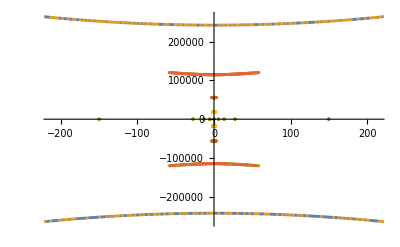

```mathematica
ListPlot[Transpose[{Im[#],Re[#]}&/@#&/@Cases[vals[[All,2;;-1]],u_/;Length[u]>M]],Joined->False]
```

Eigenvalues::argt: Eigenvalues called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Eigenvalues::argt will be suppressed during this calculation.

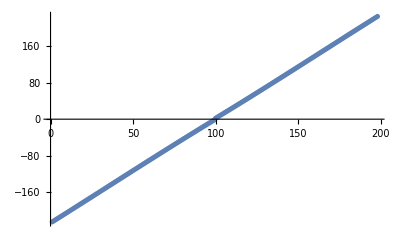
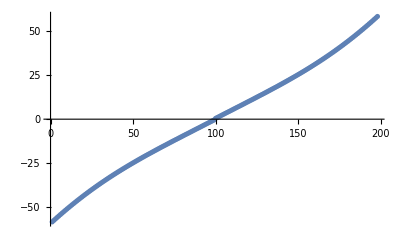
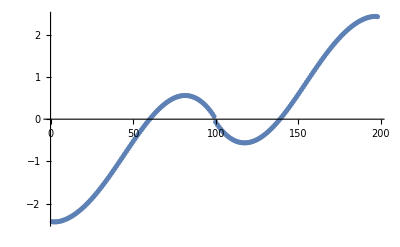
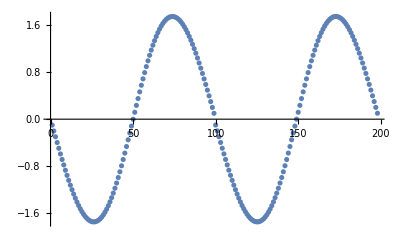
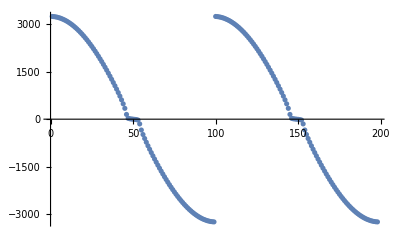
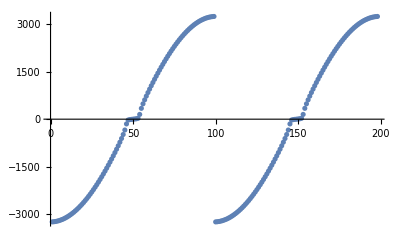
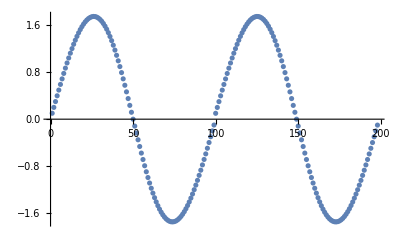
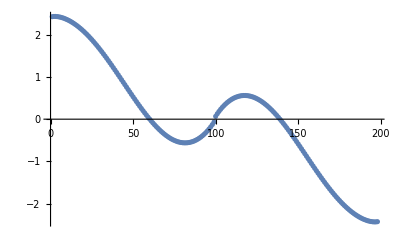

Eigenvalues::argt: Eigenvalues called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Eigenvalues::argt will be suppressed during this calculation.

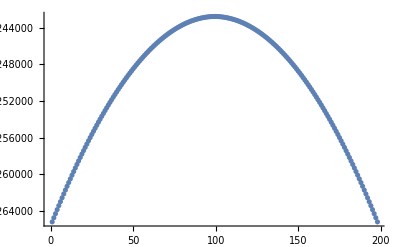
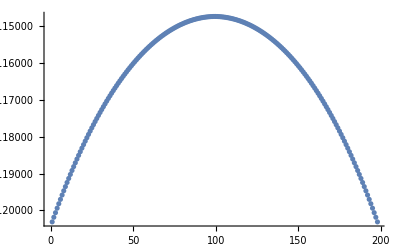
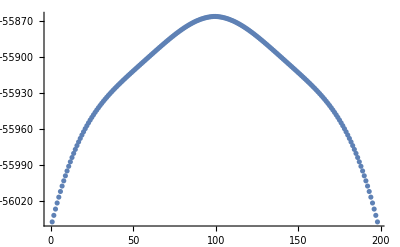
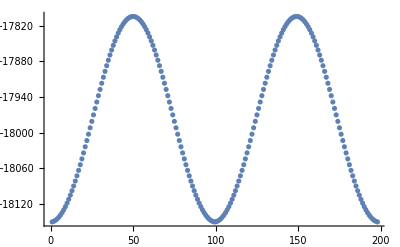
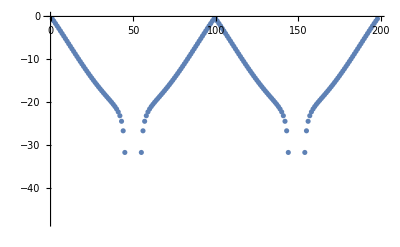
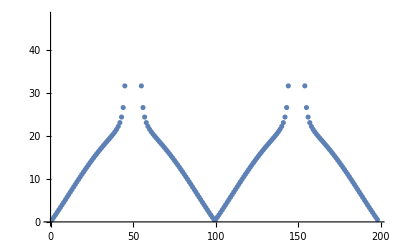
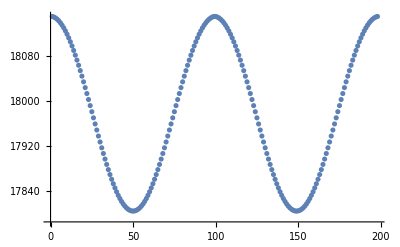
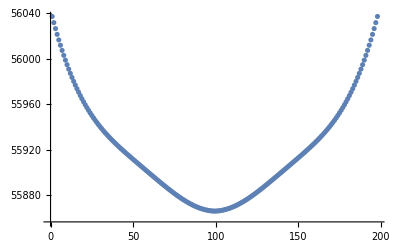

```mathematica
ListPlot[#,PlotRange->All]&/@Transpose[(Im[#]&/@#&/@(SortBy[#,Re[#]&]&/@Cases[vals[[All,2;;-1]],u_/;Length[u]>M]))]
ListPlot[#]&/@Transpose[(Re[#]&/@#&/@(SortBy[#,Re[#]&]&/@Cases[vals[[All,2;;-1]],u_/;Length[u]>M]))]
```

```mathematica
wavevector sweep
```

```mathematica
freqmin=2*Pi*15;
freqmax=2*Pi*25;
num=200;
freqs=Table[freq,{freq,freqmin,freqmax,(freqmax-freqmin)/num}];
AbsoluteTiming[subharmonic=Table[Eigenvalues[{eq1,eq2}/.g->980/.σ->20/.qy->0/.qx->2*Pi/2./.μ->0.05/.ρ->1/.h0->0.5/.ωd->freq/.ω->0.5*freq],{freq,freqs}];]
AbsoluteTiming[harmonic=Table[Eigenvalues[{eq1,eq2}/.g->980/.σ->20/.qy->0/.qx->2*Pi/1./.μ->0.05/.ρ->1/.h0->0.5/.ωd->freq/.ω->0.000001*freq],{freq,freqs}];]
```

{5.57431,Null}

{5.54553,Null}

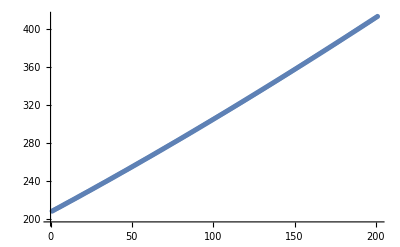
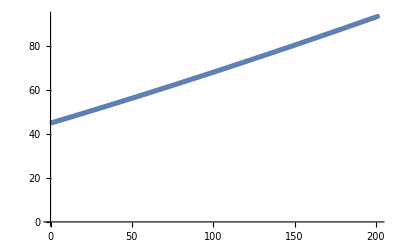
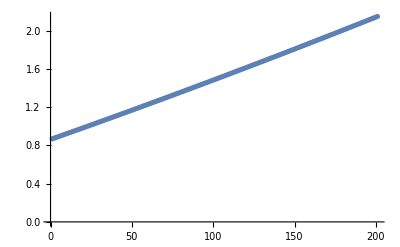
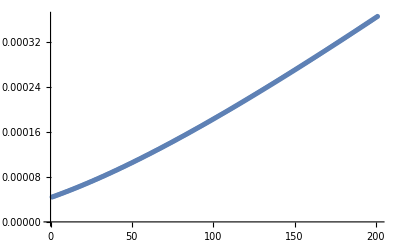
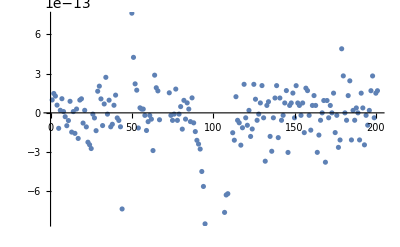
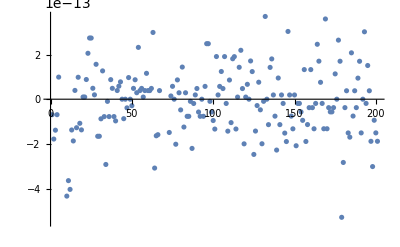
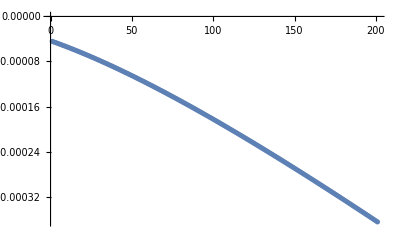
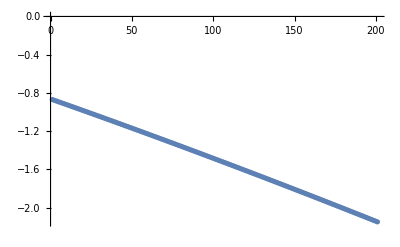
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

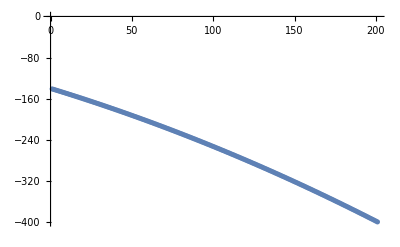
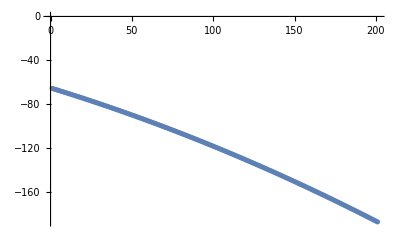
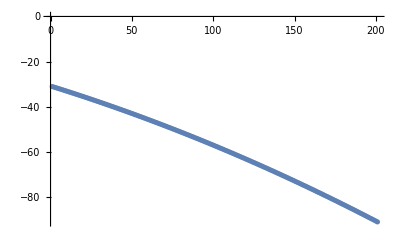
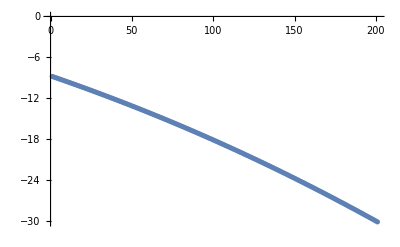
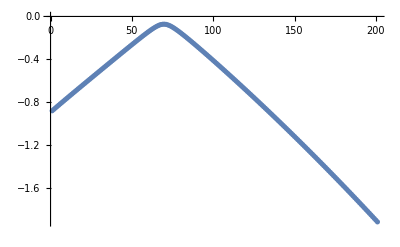
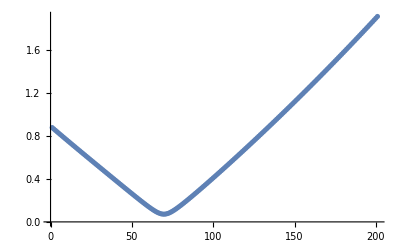
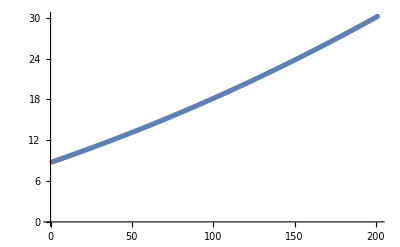
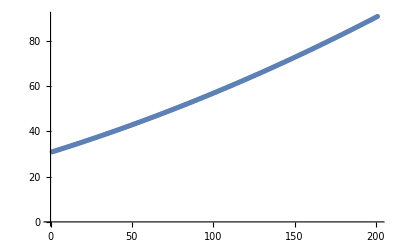
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[Im[#]]&/@(Transpose[SortBy[#,Re[#]&]&/@subharmonic])
ListPlot[Re[#]/980]&/@(Transpose[SortBy[#,Re[#]&]&/@subharmonic])
```

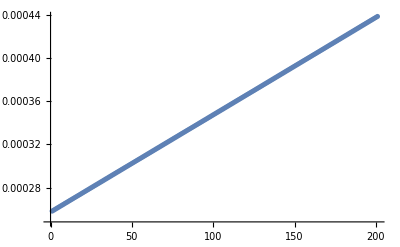
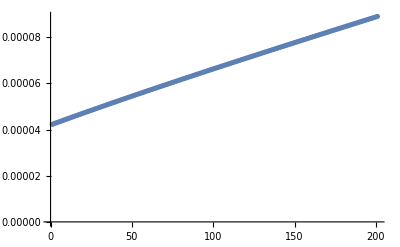
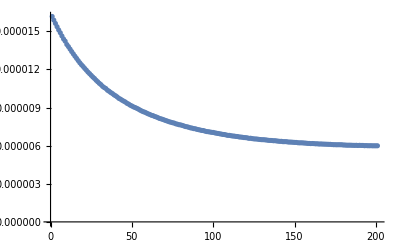
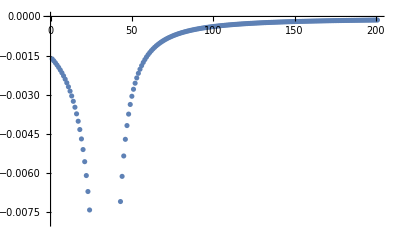
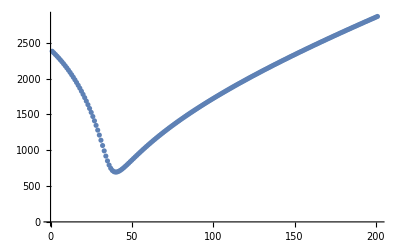
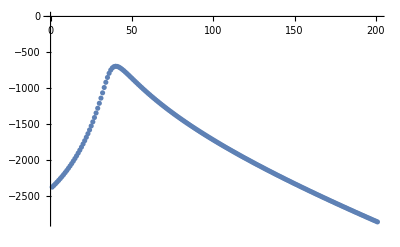
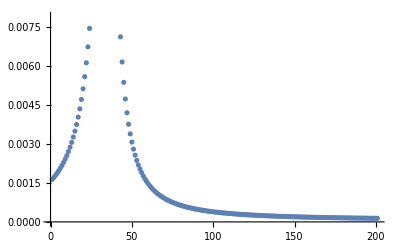
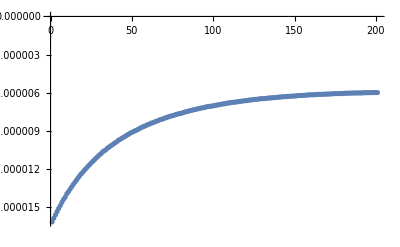
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

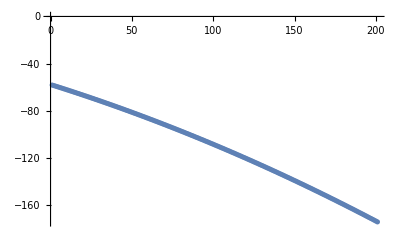
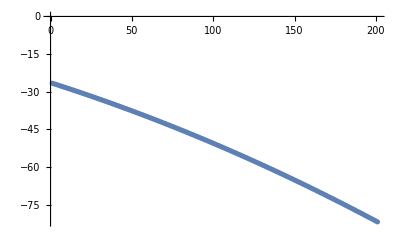
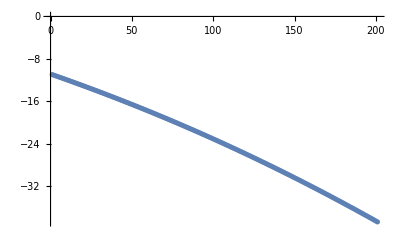
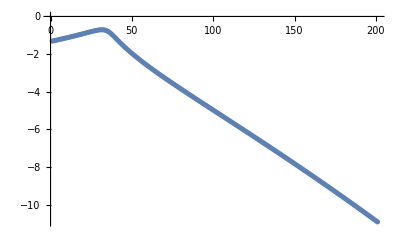
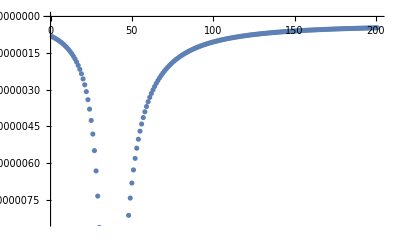
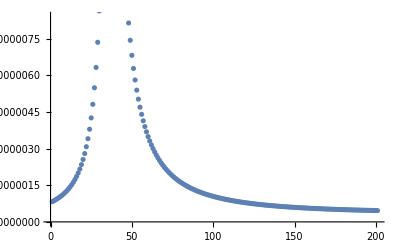
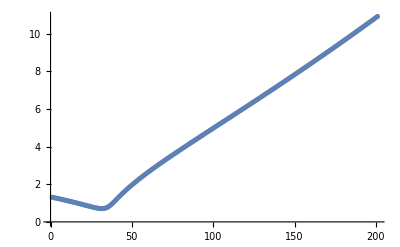
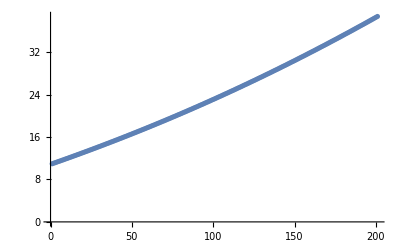
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[Im[#]]&/@(Transpose[SortBy[#,Re[#]&]&/@harmonic])
ListPlot[Re[#]/980]&/@(Transpose[SortBy[#,Re[#]&]&/@harmonic])
```

```mathematica
(* For thin flat films, the instability becomes harmonic!*)
```

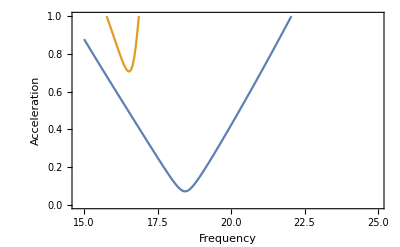

40 π

```mathematica
ListPlot[{Transpose[{freqs/(2*Pi),Re[Transpose[SortBy[#,Re[#]&]&/@subharmonic][[6]]]/980}],Transpose[{freqs/(2*Pi),Re[Transpose[SortBy[#,Re[#]&]&/@harmonic][[7]]]/980}]},PlotRange->{0,1},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]]]
```

```mathematica
wavevector sweep
```

```mathematica
qmax=2*Pi/0.5;
qmin=2*Pi/4.;
num=200;
qs=Table[q,{q,qmin,qmax,(qmax-qmin)/num}];
AbsoluteTiming[subharmonic=Table[Eigenvalues[{eq1,eq2}/.g->980/.σ->20/.qy->0/.qx->q/.μ->0.1/.ρ->1/.h0->0.5/.ωd->freq/.ω->0.5*freq],{q,qs}];]
AbsoluteTiming[harmonic=Table[Eigenvalues[{eq1,eq2}/.g->980/.σ->20/.qy->0/.qx->q/.μ->0.1/.ρ->1/.h0->0.5/.ωd->freq/.ω->0.000001*freq],{q,qs}];]
```

{5.60247,Null}

{5.53982,Null}

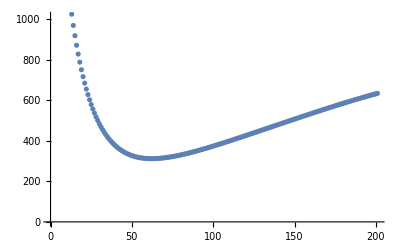
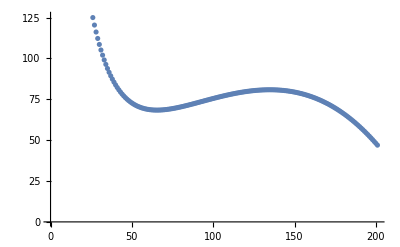
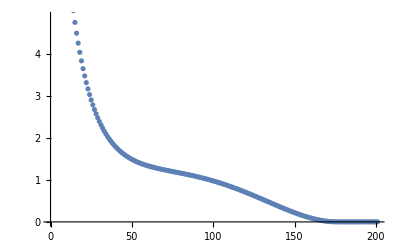
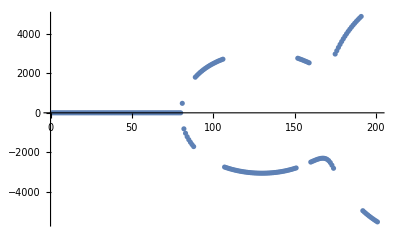
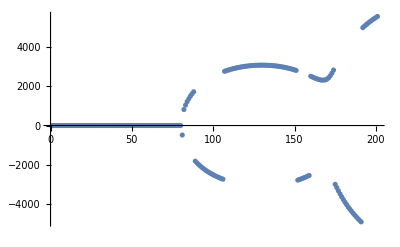
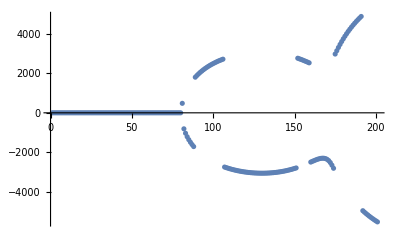
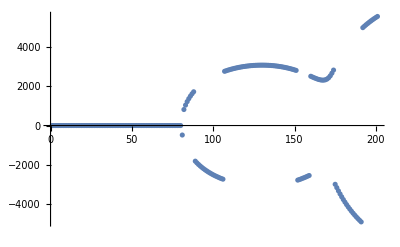
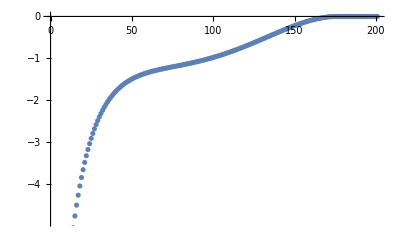
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

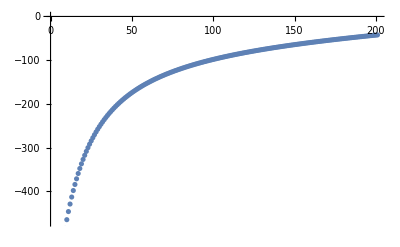
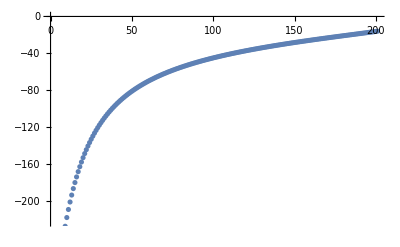
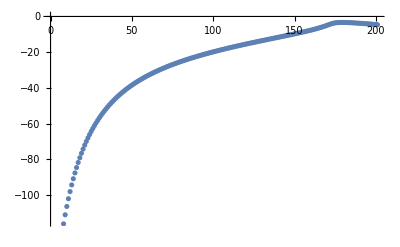
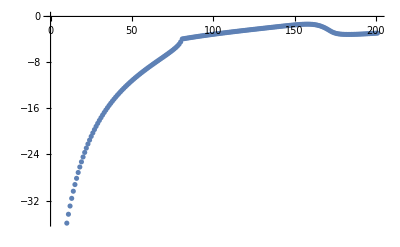
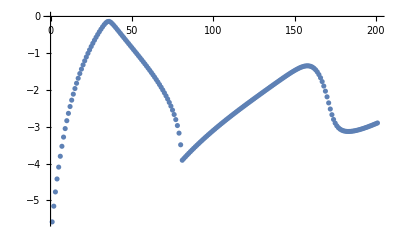
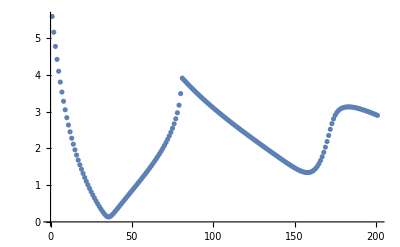
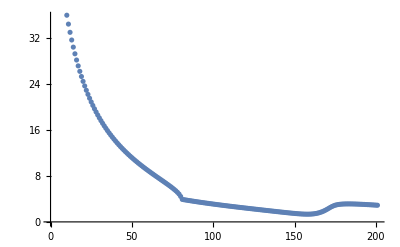
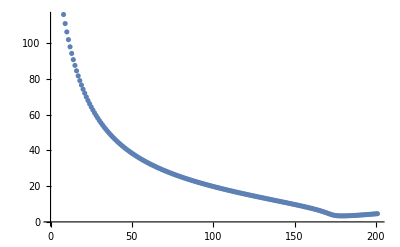
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[Im[#]]&/@(Transpose[SortBy[#,Re[#]&]&/@subharmonic])
ListPlot[Re[#]/980]&/@(Transpose[SortBy[#,Re[#]&]&/@subharmonic])
```

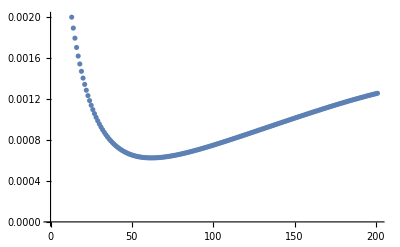
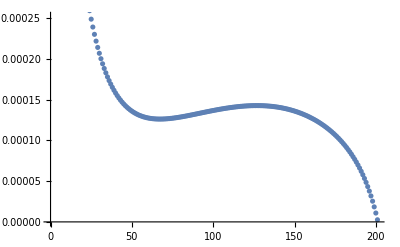
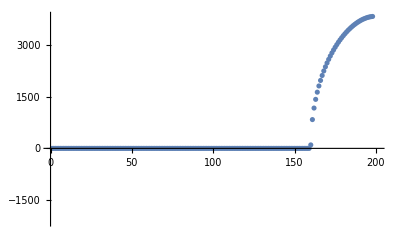
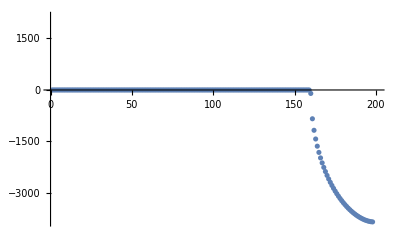
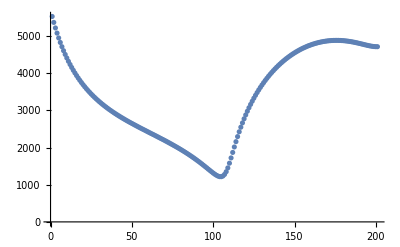
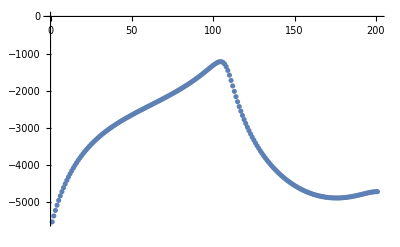
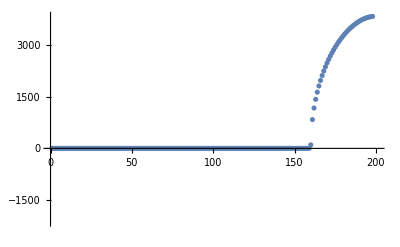
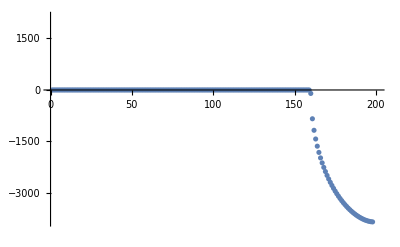
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

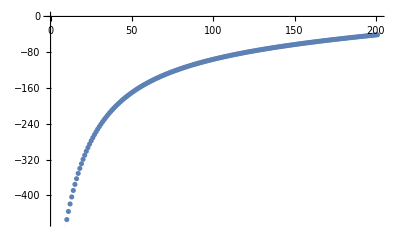
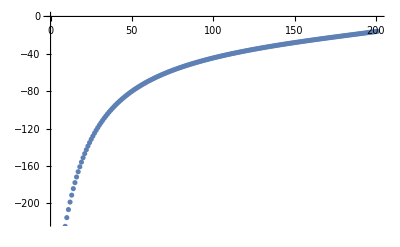
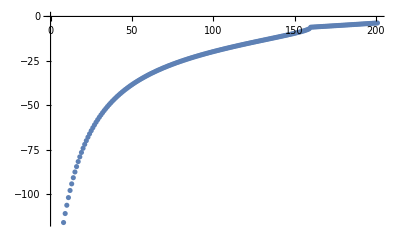
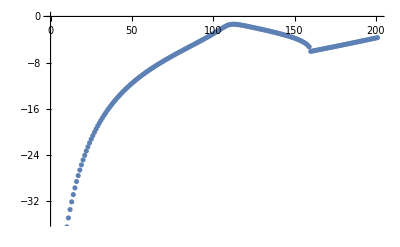
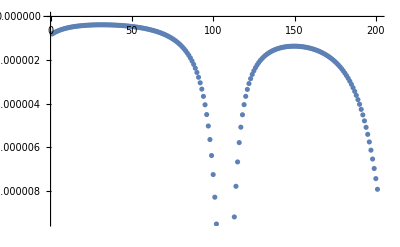
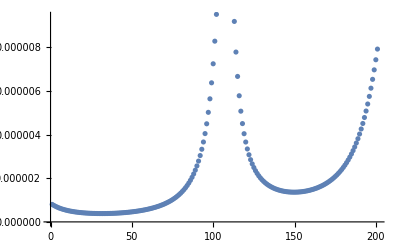
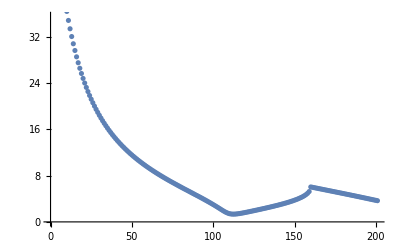
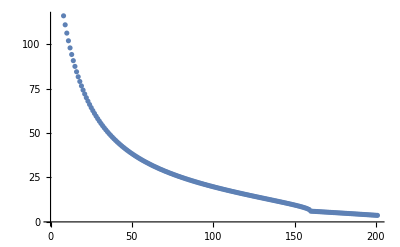
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[Im[#]]&/@(Transpose[SortBy[#,Re[#]&]&/@harmonic])
ListPlot[Re[#]/980]&/@(Transpose[SortBy[#,Re[#]&]&/@harmonic])
```

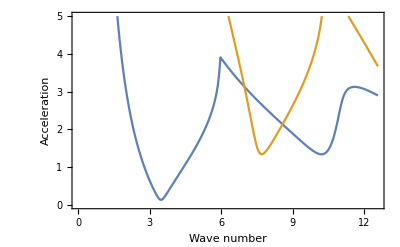

```mathematica
ListPlot[{Transpose[{qs,Re[Transpose[SortBy[#,Re[#]&]&/@subharmonic][[6]]]/980}],Transpose[{qs,Re[Transpose[SortBy[#,Re[#]&]&/@harmonic][[7]]]/980}]},PlotRange->{0,5},Joined->True,Axes->False,Frame->True,FrameLabel->{"Wave number","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]]]
```

```mathematica
freqmin=2*Pi*8;
freqmax=2*Pi*25;
num=200;
length=10;
L=length/10;
freqs=Table[freq,{freq,freqmin,freqmax,(freqmax-freqmin)/num}];
AbsoluteTiming[Monitor[subharmonic2=Table[ParallelTable[Quiet[Eigenvalues[{eq1,eq2}/.g->980/.σ->72/.qy->0/.μ->0.01/.ρ->1/.h0->1/.ωd->freq/.ω->0.5*freq]],{qx,2*Pi/length,2*Pi/L,2*Pi/length}],{freq,freqs}];,N[(freq-freqmin)/(freqmax-freqmin)]]]
AbsoluteTiming[Monitor[harmonic2=Table[ParallelTable[Quiet[Eigenvalues[{eq1,eq2}/.g->980/.σ->72/.qy->0/.μ->0.01/.ρ->1/.h0->1/.ωd->freq/.ω->0.00001*freq]],{qx,2*Pi/length,2*Pi/L,2*Pi/length}],{freq,freqs}];,N[(freq-freqmin)/(freqmax-freqmin)]]]
```

{24.0759,Null}

{19.7428,Null}

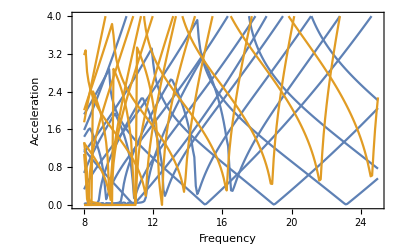

```mathematica
Show[ListPlot[Table[{#[[1]],Re[#[[2]]]/980}&/@Transpose[{freqs/(2*Pi),Transpose[SortBy[#,Re[#]&]&/@subharmonic2[[All,i]]][[4]]}],{i,1,length/L}],PlotStyle->Directive[ColorData[97,"ColorList"][[1]]],PlotRange->{0,4},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]]],ListPlot[Table[{#[[1]],Re[#[[2]]]/980}&/@Transpose[{freqs/(2*Pi),Transpose[SortBy[#,Re[#]&]&/@harmonic2[[All,i]]][[5]]}],{i,1,length/L}],PlotStyle->Directive[ColorData[97,"ColorList"][[2]]],PlotRange->{0,4},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]]]]
```

#### partial inversion

```mathematica
subs0={A->KroneckerDelta[k1,1],B->KroneckerDelta[k1,2],Ax->KroneckerDelta[k1,3],Bx->KroneckerDelta[k1,4],Ay->KroneckerDelta[k1,5],By->KroneckerDelta[k1,6],Az->KroneckerDelta[k1,7],Bz->KroneckerDelta[k1,8], H->KroneckerDelta[k1,9],kx->qx,ky->qy,ω->ω+l1*ωd};
eqs0=Transpose[Table[{Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)+z Ω)]/.subs0],Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)-z Ω)]/.subs0],(I*kx*uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]+(Exp[-I*(kx*x+ky*y+ω*t)]*D[ux[x,y,z,t],z]/.z->h0))/.z->h0/.subs0,(I*ky*uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]+(Exp[-I*(kx*x+ky*y+ω*t)]*D[uy[x,y,z,t],z]/.z->h0))/.z->h0/.subs0,Simplify[(I*ω*(h[x,y,z,t]-h0)-uz[x,y,z,t]/.z->h0)*Exp[-I*(kx*x+ky*y+ω*t)]/.subs0],Expand[(-ρ*g*(h[x,y,z,t]-h0)+(P[x,y,h0,t]+ρ*g*h0)-2*μ*(D[uz[x,y,z,t],z]/.z->h0)-σ*k^2*(h[x,y,z,t]-h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.subs0],Simplify[ux[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]/.z->0/.subs0],Simplify[uy[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]/.z->0/.subs0],Simplify[uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]/.z->0/.subs0]},{k1,1,9}]];
```

```mathematica
elim=Range[6];
perts=DeleteDuplicates[Sort/@Cases[Permutations[Range[8],Length[elim]],u_/;Length[u]==Length[elim]]];
Monitor[dets=Table[Expand[Det[eqs0[[elim,perts[[i]]]]]],{i,1,Length[perts]}];,i]
lperts=DeleteDuplicates[First/@Position[dets,u_/;u≠0]]
```

{2,3,4,5,7,8,9,10,11,12,13,14,18,19,20,21,24,25,26,27}

```mathematica
First/@subs0[[Complement[Range[9],perts[[#]]]]]&/@lperts
```

{{By,Bz,H},{By,Az,H},{Ay,Bz,H},{Ay,Az,H},{Bx,Bz,H},{Bx,Az,H},{Bx,By,H},{Bx,Ay,H},{Ax,Bz,H},{Ax,Az,H},{Ax,By,H},{Ax,Ay,H},{B,By,H},{B,Ay,H},{B,Bx,H},{B,Ax,H},{A,By,H},{A,Ay,H},{A,Bx,H},{A,Ax,H}}

```mathematica
M=5;
eqs2t=Transpose[Table[{0,0,0,0,0,-ρ*KroneckerDelta[k1,9]*(KroneckerDelta[l1+1,l2]+KroneckerDelta[l1-1,l2])/2,0,0,0},{k1,1,9}]];

ipert=lperts[[7]];
First/@subs0[[Complement[Range[9],perts[[ipert]]]]]
AbsoluteTiming[eqt=Simplify[(eqs0[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs0[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs0[[elim,perts[[ipert]]]]].eqs0[[elim,Complement[Range[9],perts[[ipert]]]]])];]
Monitor[AbsoluteTiming[eq1t=ArrayFlatten[Table[eqt*KroneckerDelta[l1,l2],{l1,-M,M},{l2,-M,M}]];],{l1,l2}]
Monitor[AbsoluteTiming[eq2t=ArrayFlatten[Table[Evaluate[FullSimplify[(eqs2t[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs0[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs0[[elim,perts[[ipert]]]]].eqs2t[[elim,Complement[Range[9],perts[[ipert]]]]])]],{l1,-M,M},{l2,-M,M}]];],{l1,l2}]
```

{Bx,By,H}

{7.98384,Null}

{0.102513,Null}

{2.00868,Null}

```mathematica
Simplify[FullSimplify[(eqs0[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs0[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs0[[elim,perts[[ipert]]]]].eqs0[[elim,Complement[Range[9],perts[[ipert]]]]]) /. ω->(Ω1[l1]^2-qx^2-qy^2)/(I*ρ/μ)-l1*ωd,Ω1[l1]>0&&κ>0]/.qx^2->κ^2-qy^2,κ>0]

FullSimplify[FullSimplify[(eqs2t[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs0[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs0[[elim,perts[[ipert]]]]].eqs2t[[elim,Complement[Range[9],perts[[ipert]]]]])/. ω->(Ω1[l1]^2-qx^2-qy^2)/(I*ρ/μ)-l1*ωd,Ω1[l1]>0&&κ>0]/.qx^2->κ^2-qy^2]
```

{{2 ⅇ^(-h0 Ω1[l1]) (Cosh[h0 Ω1[l1]]+(2 (qy^2-κ^2) Cosh[h0 κ])/(κ^2+Ω1[l1]^2)),-(4 ⅇ^(-h0 Ω1[l1]) qx qy Cosh[h0 κ])/(κ^2+Ω1[l1]^2),-1/(2 κ μ ρ (κ^2+Ω1[l1]^2))ⅈ ⅇ^(-h0 (κ+Ω1[l1])) qx (2 ⅇ^(h0 (κ+Ω1[l1])) κ (ρ (g ρ+κ^2 σ) Cosh[h0 κ]+κ^3 μ^2 Sinh[h0 κ])-4 (-ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^3 μ^2 Ω1[l1]+2 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^2 μ^2 Ω1[l1]^2+4 ⅇ^(h0 κ) κ μ^2 Ω1[l1]^3+ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)},{-(4 ⅇ^(-h0 Ω1[l1]) qx qy Cosh[h0 κ])/(κ^2+Ω1[l1]^2),2 ⅇ^(-h0 Ω1[l1]) (Cosh[h0 Ω1[l1]]-(2 qy^2 Cosh[h0 κ])/(κ^2+Ω1[l1]^2)),-1/(2 κ μ ρ (κ^2+Ω1[l1]^2))ⅈ ⅇ^(-h0 (κ+Ω1[l1])) qy (2 ⅇ^(h0 (κ+Ω1[l1])) κ (ρ (g ρ+κ^2 σ) Cosh[h0 κ]+κ^3 μ^2 Sinh[h0 κ])-4 (-ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^3 μ^2 Ω1[l1]+2 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^2 μ^2 Ω1[l1]^2+4 ⅇ^(h0 κ) κ μ^2 Ω1[l1]^3+ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)},{4 ⅈ ⅇ^(-h0 Ω1[l1]) qx (Sinh[h0 Ω1[l1]]/(2 Ω1[l1])-(κ Sinh[h0 κ])/(κ^2+Ω1[l1]^2)),4 ⅈ ⅇ^(-h0 Ω1[l1]) qy (Sinh[h0 Ω1[l1]]/(2 Ω1[l1])-(κ Sinh[h0 κ])/(κ^2+Ω1[l1]^2)),1/(2 μ ρ (κ^2+Ω1[l1]^2))ⅇ^(-h0 (κ+Ω1[l1])) (-4 ⅇ^(h0 κ) κ^4 μ^2+ⅇ^(h0 Ω1[l1]) κ (κ^3 μ^2-g ρ^2-κ^2 ρ σ)+ⅇ^(h0 (2 κ+Ω1[l1])) κ (κ^3 μ^2+g ρ^2+κ^2 ρ σ)-4 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^3 μ^2 Ω1[l1]+2 (-2 ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^2 μ^2 Ω1[l1]^2+ⅇ^(h0 Ω1[l1]) (1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)}}

{{0,0,-(ⅈ qx ρ Cosh[h0 κ] (-1+l1,l2+1+l1,l2))/(2 μ (κ^2+Ω1[l1]^2))},{0,0,-(ⅈ qy ρ Cosh[h0 κ] (-1+l1,l2+1+l1,l2))/(2 μ (κ^2+Ω1[l1]^2))},{0,0,(κ ρ (-1+l1,l2+1+l1,l2) Sinh[h0 κ])/(2 μ (κ^2+Ω1[l1]^2))}}

```mathematica
freq=2*Pi*26;
syst={eq1t,eq2t}/.g->980/.σ->72/.qx->2*Pi/(2)/.qy->-2*Pi/(2*3^(1/2))/.μ->0.01/.ρ->1/.h0->0.5/.ωd->freq/.ω->0.5*freq;
AbsoluteTiming[{evalsbase,evecsbase}=Eigensystem[syst];]
AbsoluteTiming[{evalsbase2,evecsbase2}=Eigensystem[Conjugate[Transpose[#]]&/@syst];]
evalsbase
evalsbase2
```

{0.001131,Null}

{0.001286,Null}

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,350543.-134.857 ⅈ,-350543.+134.857 ⅈ,163493.-29.9634 ⅈ,-163493.+29.9634 ⅈ,-78489.8+0.640618 ⅈ,78489.8-0.640618 ⅈ,24492.4-0.0000675186 ⅈ,-24492.4+0.0000675186 ⅈ,51.8327-9.3049×10^-13 ⅈ,-51.8327-5.66636×10^-13 ⅈ}

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,7.55783×10^17+1.50818×10^16 ⅈ,7.21179×10^17+3.71361×10^15 ⅈ,2.84251×10^17-2.68848×10^15 ⅈ,6.32474×10^16-1.51401×10^15 ⅈ,5.83585×10^16+1.19245×10^15 ⅈ,350543.+134.857 ⅈ,-350543.-134.857 ⅈ,163493.+29.9634 ⅈ,-163493.-29.9634 ⅈ,-78489.8-0.640618 ⅈ,78489.8+0.640618 ⅈ,24492.4+0.0000675187 ⅈ,-24492.4-0.0000675185 ⅈ,-51.8327-2.40477×10^-12 ⅈ,51.8327+1.67707×10^-12 ⅈ}

### periodic

```mathematica
subs1={A->KroneckerDelta[k1,1]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],B->KroneckerDelta[k1,2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Ax->KroneckerDelta[k1,3]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Bx->KroneckerDelta[k1,4]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Ay->KroneckerDelta[k1,5]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],By->KroneckerDelta[k1,6]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Az->KroneckerDelta[k1,7]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Bz->KroneckerDelta[k1,8]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2], H->KroneckerDelta[k1,9]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2]};
subs2={kx->qx+n1*q1.{1,0}+m1*q2.{1,0},ky->qy+n1*q1.{0,1}+m1*q2.{0,1},ω->ω+l1*ωd};
eqs1=Transpose[Table[{Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)+z Ω)]/.subs1/.subs2],Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)-z Ω)]/.subs1/.subs2],(I*kx*uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]+(Exp[-I*(kx*x+ky*y+ω*t)]*D[ux[x,y,z,t],z]/.z->h0))/.z->h0/.subs1/.subs2,(I*ky*uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]+(Exp[-I*(kx*x+ky*y+ω*t)]*D[uy[x,y,z,t],z]/.z->h0))/.z->h0/.subs1/.subs2,Simplify[(I*ω*(h[x,y,z,t]-h0)-uz[x,y,z,t]/.z->h0)*Exp[-I*(kx*x+ky*y+ω*t)]/.subs1/.subs2],Expand[(-ρ*g*(h[x,y,z,t]-h0)+(P[x,y,h0,t]+ρ*g*h0)-2*μ*(D[uz[x,y,z,t],z]/.z->h0)-σ*k^2*(h[x,y,z,t]-h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.subs1/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,3]+KroneckerDelta[k1,4]*(-1)^(n1-n2+m1-m2))*BesselI[n1-n2,Ω*as/2]*BesselI[m1-m2,Ω*as/2]-kx/(ρ*ω)*(KroneckerDelta[k1,1]+KroneckerDelta[k1,2]*(-1)^(n1-n2+m1-m2))*BesselI[n1-n2,k*as/2]*BesselI[m1-m2,k*as/2])/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,5]+KroneckerDelta[k1,6]*(-1)^(n1-n2+m1-m2))*BesselI[n1-n2,Ω*as/2]*BesselI[m1-m2,Ω*as/2]-ky/(ρ*ω)*(KroneckerDelta[k1,1]+KroneckerDelta[k1,2]*(-1)^(n1-n2+m1-m2))*BesselI[n1-n2,k*as/2]*BesselI[m1-m2,k*as/2])/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,7]+KroneckerDelta[k1,8]*(-1)^(n1-n2+m1-m2))*BesselI[n1-n2,Ω*as/2]*BesselI[m1-m2,Ω*as/2]+I*k/(ρ*ω)*(KroneckerDelta[k1,1]-KroneckerDelta[k1,2]*(-1)^(n1-n2+m1-m2))*BesselI[n1-n2,k*as/2]*BesselI[m1-m2,k*as/2])/.subs2]},{k1,1,9}]];
```

{{0,0,ⅈ (qx+n1 q1.{1,0}+m1 q2.{1,0}) l1,l2 m1,m2 n1,n2,0,ⅈ (qy+n1 q1.{0,1}+m1 q2.{0,1}) l1,l2 m1,m2 n1,n2,0,√((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,0,0},{0,0,0,ⅈ (qx+n1 q1.{1,0}+m1 q2.{1,0}) l1,l2 m1,m2 n1,n2,0,ⅈ (qy+n1 q1.{0,1}+m1 q2.{0,1}) l1,l2 m1,m2 n1,n2,0,-√((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,0},{-1/(ρ (ω+l1 ωd))2 ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (qx+n1 q1.{1,0}+m1 q2.{1,0}) √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,1/(ρ (ω+l1 ωd))2 ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (qx+n1 q1.{1,0}+m1 q2.{1,0}) √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,-ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,0,0,ⅈ ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (qx+n1 q1.{1,0}+m1 q2.{1,0}) l1,l2 m1,m2 n1,n2,ⅈ ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (qx+n1 q1.{1,0}+m1 q2.{1,0}) l1,l2 m1,m2 n1,n2,0},{-1/(ρ (ω+l1 ωd))2 ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (qy+n1 q1.{0,1}+m1 q2.{0,1}) √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,1/(ρ (ω+l1 ωd))2 ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (qy+n1 q1.{0,1}+m1 q2.{0,1}) √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,0,0,ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,-ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,ⅈ ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (qy+n1 q1.{0,1}+m1 q2.{0,1}) l1,l2 m1,m2 n1,n2,ⅈ ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (qy+n1 q1.{0,1}+m1 q2.{0,1}) l1,l2 m1,m2 n1,n2,0},{-1/(ρ (ω+l1 ωd))ⅈ ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,1/(ρ (ω+l1 ωd))ⅈ ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,0,0,0,0,-ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) l1,l2 m1,m2 n1,n2,-ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) l1,l2 m1,m2 n1,n2,ⅈ (ω+l1 ωd) l1,l2 m1,m2 n1,n2},{ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) l1,l2 m1,m2 n1,n2-(2 ⅈ ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) qx^2 μ l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(2 ⅈ ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) qy^2 μ l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(4 ⅈ ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) n1 qy μ q1.{0,1} l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(2 ⅈ ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) n1^2 μ (q1.{0,1})^2 l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(4 ⅈ ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) n1 qx μ q1.{1,0} l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(2 ⅈ ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) n1^2 μ (q1.{1,0})^2 l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(4 ⅈ ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) m1 qy μ q2.{0,1} l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(4 ⅈ ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) m1 n1 μ q1.{0,1} q2.{0,1} l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(2 ⅈ ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) m1^2 μ (q2.{0,1})^2 l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(4 ⅈ ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) m1 qx μ q2.{1,0} l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(4 ⅈ ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) m1 n1 μ q1.{1,0} q2.{1,0} l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(2 ⅈ ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) m1^2 μ (q2.{1,0})^2 l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd)),ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) l1,l2 m1,m2 n1,n2-(2 ⅈ ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) qx^2 μ l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(2 ⅈ ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) qy^2 μ l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(4 ⅈ ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) n1 qy μ q1.{0,1} l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(2 ⅈ ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) n1^2 μ (q1.{0,1})^2 l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(4 ⅈ ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) n1 qx μ q1.{1,0} l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(2 ⅈ ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) n1^2 μ (q1.{1,0})^2 l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(4 ⅈ ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) m1 qy μ q2.{0,1} l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(4 ⅈ ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) m1 n1 μ q1.{0,1} q2.{0,1} l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(2 ⅈ ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) m1^2 μ (q2.{0,1})^2 l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(4 ⅈ ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) m1 qx μ q2.{1,0} l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(4 ⅈ ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) m1 n1 μ q1.{1,0} q2.{1,0} l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd))-(2 ⅈ ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) m1^2 μ (q2.{1,0})^2 l1,l2 m1,m2 n1,n2)/(ρ (ω+l1 ωd)),0,0,0,0,-2 ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) μ √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,2 ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) μ √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,-g ρ l1,l2 m1,m2 n1,n2-qx^2 σ l1,l2 m1,m2 n1,n2-qy^2 σ l1,l2 m1,m2 n1,n2-2 n1 qy σ q1.{0,1} l1,l2 m1,m2 n1,n2-n1^2 σ (q1.{0,1})^2 l1,l2 m1,m2 n1,n2-2 n1 qx σ q1.{1,0} l1,l2 m1,m2 n1,n2-n1^2 σ (q1.{1,0})^2 l1,l2 m1,m2 n1,n2-2 m1 qy σ q2.{0,1} l1,l2 m1,m2 n1,n2-2 m1 n1 σ q1.{0,1} q2.{0,1} l1,l2 m1,m2 n1,n2-m1^2 σ (q2.{0,1})^2 l1,l2 m1,m2 n1,n2-2 m1 qx σ q2.{1,0} l1,l2 m1,m2 n1,n2-2 m1 n1 σ q1.{1,0} q2.{1,0} l1,l2 m1,m2 n1,n2-m1^2 σ (q2.{1,0})^2 l1,l2 m1,m2 n1,n2},{-1/(ρ (ω+l1 ωd))BesselI[m1-m2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] (qx+n1 q1.{1,0}+m1 q2.{1,0}) l1,l2,-1/(ρ (ω+l1 ωd))(-1)^(m1-m2+n1-n2) BesselI[m1-m2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] (qx+n1 q1.{1,0}+m1 q2.{1,0}) l1,l2,BesselI[m1-m2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] l1,l2,(-1)^(m1-m2+n1-n2) BesselI[m1-m2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] l1,l2,0,0,0,0,0},{-1/(ρ (ω+l1 ωd))BesselI[m1-m2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] (qy+n1 q1.{0,1}+m1 q2.{0,1}) l1,l2,-1/(ρ (ω+l1 ωd))(-1)^(m1-m2+n1-n2) BesselI[m1-m2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] (qy+n1 q1.{0,1}+m1 q2.{0,1}) l1,l2,0,0,BesselI[m1-m2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] l1,l2,(-1)^(m1-m2+n1-n2) BesselI[m1-m2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] l1,l2,0,0,0},{1/(ρ (ω+l1 ωd))ⅈ BesselI[m1-m2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2,-1/(ρ (ω+l1 ωd))ⅈ (-1)^(m1-m2+n1-n2) BesselI[m1-m2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2,0,0,0,0,BesselI[m1-m2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] l1,l2,(-1)^(m1-m2+n1-n2) BesselI[m1-m2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] l1,l2,0}}

```mathematica
Simplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[1]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-eqs1[[1]]]
Simplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[2]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-eqs1[[2]]]
Simplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[3]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-eqs1[[3]]]
Simplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[4]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-eqs1[[4]]]
Simplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[5]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-eqs1[[5]]]
Simplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[6]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-eqs1[[6]]]
FullSimplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[7]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-(eqs1[[7]]/.as->0)/.BesselI[a_-b_,0]:>KroneckerDelta[a,b]]
FullSimplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[8]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-(eqs1[[8]]/.as->0)/.BesselI[a_-b_,0]:>KroneckerDelta[a,b]]
FullSimplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[9]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-(eqs1[[9]]/.as->0)/.BesselI[a_-b_,0]:>KroneckerDelta[a,b]]
```

{0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0}

«6 more identical outputs»

```mathematica
Clear[q1];
Clear[q2];

elim=Range[6];
perts=DeleteDuplicates[Sort/@Cases[Permutations[Range[8],Length[elim]],u_/;Length[u]==Length[elim]]];
Monitor[dets=Table[Expand[Det[eqs1[[elim,perts[[i]]]]]],{i,1,Length[perts]}];,i]
lperts=DeleteDuplicates[First/@Position[dets,u_/;Abs[u]≠0.]]
```

{2,3,4,5,7,8,9,10,11,12,13,14,18,19,20,21,24,25,26,27}

```mathematica
ipert=lperts[[7]]
First/@subs0[[Complement[Range[9],perts[[ipert]]]]]
```

9

{Bx,By,H}

```mathematica
First/@subs0[[Complement[Range[9],perts[[#]]]]]&/@lperts
```

{{By,Bz,H},{By,Az,H},{Ay,Bz,H},{Ay,Az,H},{Bx,Bz,H},{Bx,Az,H},{Bx,By,H},{Bx,Ay,H},{Ax,Bz,H},{Ax,Az,H},{Ax,By,H},{Ax,Ay,H},{B,By,H},{B,Ay,H},{B,Bx,H},{B,Ax,H},{A,By,H},{A,Ay,H},{A,Bx,H},{A,Ax,H}}

```mathematica
FullSimplify[Simplify[eqs1[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs1[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs1[[elim,perts[[ipert]]]]/.m2->m1/.n2->n1/.l2->l1].(eqs1[[elim,Complement[Range[9],perts[[ipert]]]]]/.m2->m1/.n2->n1/.l2->l1)/.
BesselI[m1-m2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)]->I1[m1-m2,n1,m1]/.BesselI[n1-n2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)]->I1[n1-n2,n1,m1]/.BesselI[m1-m2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)]->I2[m1-m2,n1,m1,l1]/.BesselI[n1-n2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)]->I2[n1-n2,n1,m1,l1]/.qx->(κx-n1 q1.{1,0}-m1 q2.{1,0})/.qy->(κy-n1 q1.{0,1}-m1 q2.{0,1})/.ω->-I*μ/ρ*(Ω1[n1,m1,l1]^2-κx^2-κy^2)-l1 ωd/.κx^2->κ[n1,m1]^2-κy^2,κ[n1,m1]>0&&Ω1[n1,m1,l1]>0]/.κx^2->κ[n1,m1]^2-κy^2/.κx->κx[n1,m1]/.κy->κy[n1,m1]/.l2->l1]
```

{{1/(κ[n1,m1]^2+Ω1[n1,m1,l1]^2)(-1)^(-m2-n2) ⅇ^(-h0 (κ[n1,m1]+2 Ω1[n1,m1,l1])) (-2 ((-1)^(m2+n2) ⅇ^(h0 Ω1[n1,m1,l1])+(-1)^(m1+n1) ⅇ^(h0 (2 κ[n1,m1]+Ω1[n1,m1,l1]))) I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] (κ[n1,m1]^2-κy[n1,m1]^2)+((-1)^(m2+n2) ⅇ^(h0 κ[n1,m1])+(-1)^(m1+n1) ⅇ^(h0 (κ[n1,m1]+2 Ω1[n1,m1,l1]))) I2[m1-m2,n1,m1,l1] I2[n1-n2,n1,m1,l1] (κ[n1,m1]^2+Ω1[n1,m1,l1]^2)),-(2 (-1)^(-m2-n2) ⅇ^(-h0 (κ[n1,m1]+Ω1[n1,m1,l1])) ((-1)^(m2+n2)+(-1)^(m1+n1) ⅇ^(2 h0 κ[n1,m1])) I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] κx[n1,m1] κy[n1,m1])/(κ[n1,m1]^2+Ω1[n1,m1,l1]^2),-1/(2 μ ρ)ⅈ ⅇ^(-h0 (κ[n1,m1]+Ω1[n1,m1,l1])) κx[n1,m1] (4 ⅇ^(h0 κ[n1,m1]) μ^2 I2[m1-m2,n1,m1,l1] I2[n1-n2,n1,m1,l1] Ω1[n1,m1,l1]+((-1)^(-m2-n2) I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] ((-1)^(m2+n2) ⅇ^(h0 Ω1[n1,m1,l1]) (g ρ^2 κ[n1,m1]-μ^2 κ[n1,m1]^4-2 μ^2 κ[n1,m1]^2 Ω1[n1,m1,l1]^2-μ^2 Ω1[n1,m1,l1]^4+κ[n1,m1]^3 (ρ σ-4 μ^2 Ω1[n1,m1,l1]))+(-1)^(m1+n1) ⅇ^(h0 (2 κ[n1,m1]+Ω1[n1,m1,l1])) (g ρ^2 κ[n1,m1]+μ^2 κ[n1,m1]^4+2 μ^2 κ[n1,m1]^2 Ω1[n1,m1,l1]^2+μ^2 Ω1[n1,m1,l1]^4+κ[n1,m1]^3 (ρ σ-4 μ^2 Ω1[n1,m1,l1]))))/(κ[n1,m1] (κ[n1,m1]^2+Ω1[n1,m1,l1]^2)))},{-(2 (-1)^(-m2-n2) ⅇ^(-h0 (κ[n1,m1]+Ω1[n1,m1,l1])) ((-1)^(m2+n2)+(-1)^(m1+n1) ⅇ^(2 h0 κ[n1,m1])) I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] κx[n1,m1] κy[n1,m1])/(κ[n1,m1]^2+Ω1[n1,m1,l1]^2),1/(κ[n1,m1]^2+Ω1[n1,m1,l1]^2)(-1)^(-m2-n2) ⅇ^(-h0 (κ[n1,m1]+2 Ω1[n1,m1,l1])) (-2 ((-1)^(m2+n2) ⅇ^(h0 Ω1[n1,m1,l1])+(-1)^(m1+n1) ⅇ^(h0 (2 κ[n1,m1]+Ω1[n1,m1,l1]))) I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] κy[n1,m1]^2+((-1)^(m2+n2) ⅇ^(h0 κ[n1,m1])+(-1)^(m1+n1) ⅇ^(h0 (κ[n1,m1]+2 Ω1[n1,m1,l1]))) I2[m1-m2,n1,m1,l1] I2[n1-n2,n1,m1,l1] (κ[n1,m1]^2+Ω1[n1,m1,l1]^2)),-1/(2 μ ρ)ⅈ ⅇ^(-h0 (κ[n1,m1]+Ω1[n1,m1,l1])) κy[n1,m1] (4 ⅇ^(h0 κ[n1,m1]) μ^2 I2[m1-m2,n1,m1,l1] I2[n1-n2,n1,m1,l1] Ω1[n1,m1,l1]+((-1)^(-m2-n2) I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] ((-1)^(m2+n2) ⅇ^(h0 Ω1[n1,m1,l1]) (g ρ^2 κ[n1,m1]-μ^2 κ[n1,m1]^4-2 μ^2 κ[n1,m1]^2 Ω1[n1,m1,l1]^2-μ^2 Ω1[n1,m1,l1]^4+κ[n1,m1]^3 (ρ σ-4 μ^2 Ω1[n1,m1,l1]))+(-1)^(m1+n1) ⅇ^(h0 (2 κ[n1,m1]+Ω1[n1,m1,l1])) (g ρ^2 κ[n1,m1]+μ^2 κ[n1,m1]^4+2 μ^2 κ[n1,m1]^2 Ω1[n1,m1,l1]^2+μ^2 Ω1[n1,m1,l1]^4+κ[n1,m1]^3 (ρ σ-4 μ^2 Ω1[n1,m1,l1]))))/(κ[n1,m1] (κ[n1,m1]^2+Ω1[n1,m1,l1]^2)))},{-((ⅈ (-1)^(-m2-n2) ⅇ^(-h0 (κ[n1,m1]+2 Ω1[n1,m1,l1])) κx[n1,m1] (-2 ((-1)^(m2+n2) ⅇ^(h0 Ω1[n1,m1,l1])-(-1)^(m1+n1) ⅇ^(h0 (2 κ[n1,m1]+Ω1[n1,m1,l1]))) I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] κ[n1,m1] Ω1[n1,m1,l1]+((-1)^(m2+n2) ⅇ^(h0 κ[n1,m1])-(-1)^(m1+n1) ⅇ^(h0 (κ[n1,m1]+2 Ω1[n1,m1,l1]))) I2[m1-m2,n1,m1,l1] I2[n1-n2,n1,m1,l1] (κ[n1,m1]^2+Ω1[n1,m1,l1]^2)))/(Ω1[n1,m1,l1] (κ[n1,m1]^2+Ω1[n1,m1,l1]^2))),-((ⅈ (-1)^(-m2-n2) ⅇ^(-h0 (κ[n1,m1]+2 Ω1[n1,m1,l1])) κy[n1,m1] (-2 ((-1)^(m2+n2) ⅇ^(h0 Ω1[n1,m1,l1])-(-1)^(m1+n1) ⅇ^(h0 (2 κ[n1,m1]+Ω1[n1,m1,l1]))) I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] κ[n1,m1] Ω1[n1,m1,l1]+((-1)^(m2+n2) ⅇ^(h0 κ[n1,m1])-(-1)^(m1+n1) ⅇ^(h0 (κ[n1,m1]+2 Ω1[n1,m1,l1]))) I2[m1-m2,n1,m1,l1] I2[n1-n2,n1,m1,l1] (κ[n1,m1]^2+Ω1[n1,m1,l1]^2)))/(Ω1[n1,m1,l1] (κ[n1,m1]^2+Ω1[n1,m1,l1]^2))),1/(2 μ ρ)ⅇ^(-h0 (κ[n1,m1]+Ω1[n1,m1,l1])) (-4 ⅇ^(h0 κ[n1,m1]) μ^2 I2[m1-m2,n1,m1,l1] I2[n1-n2,n1,m1,l1] κ[n1,m1]^2+1/(κ[n1,m1]^2+Ω1[n1,m1,l1]^2)(-1)^(-m2-n2) I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] ((-1)^(m1+n1) ⅇ^(h0 (2 κ[n1,m1]+Ω1[n1,m1,l1])) (g ρ^2 κ[n1,m1]+μ^2 κ[n1,m1]^4+2 μ^2 κ[n1,m1]^2 Ω1[n1,m1,l1]^2+μ^2 Ω1[n1,m1,l1]^4+κ[n1,m1]^3 (ρ σ-4 μ^2 Ω1[n1,m1,l1]))+(-1)^(m2+n2) ⅇ^(h0 Ω1[n1,m1,l1]) (-g ρ^2 κ[n1,m1]+μ^2 κ[n1,m1]^4+2 μ^2 κ[n1,m1]^2 Ω1[n1,m1,l1]^2+μ^2 Ω1[n1,m1,l1]^4+κ[n1,m1]^3 (-ρ σ+4 μ^2 Ω1[n1,m1,l1]))))}}

```mathematica
M=5;

ipert=lperts[[7]];
First/@subs0[[Complement[Range[9],perts[[ipert]]]]]
AbsoluteTiming[eq=Simplify[(eqs1[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs1[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs1[[elim,perts[[ipert]]]]/.m2->m1/.n2->n1/.l2->l1].(eqs1[[elim,Complement[Range[9],perts[[ipert]]]]]/.m2->m1/.n2->n1/.l2->l1))];]
```

{Bx,By,H}

$Aborted

```mathematica
Simplify[(eqs1[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs1[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs1[[elim,perts[[ipert]]]]].eqs1[[elim,Complement[Range[9],perts[[ipert]]]]])]
```

```mathematica
Simplify[eq/.
BesselI[m1-m2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)]->I1[m1-m2,n1,m1]/.BesselI[n1-n2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)]->I1[n1-n2,n1,m1]/.BesselI[m1-m2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)]->I2[m1-m2,n1,m1,l1]/.BesselI[n1-n2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)]->I2[n1-n2,n1,m1,l1]/.qx->(κx-n1 q1.{1,0}-m1 q2.{1,0})/.qy->(κy-n1 q1.{0,1}-m1 q2.{0,1})/.ω->-I*μ/ρ*(Ω1[n1,m1,l1]^2-κx^2-κy^2)-l1 ωd/.κx^2->κ[n1,m1]^2-κy^2,κ[n1,m1]>0&&Ω1[n1,m1,l1]>0]/.κx^2->κ[n1,m1]^2-κy^2/.κx->κx[n1,m1]/.κy->κy[n1,m1]/.l1->l2
```

```mathematica
Simplify[FullSimplify[(eqs0[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs0[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs0[[elim,perts[[ipert]]]]].eqs0[[elim,Complement[Range[9],perts[[ipert]]]]]) /. ω->(Ω1[l1]^2-qx^2-qy^2)/(I*ρ/μ)-l1*ωd,Ω1[l1]>0&&κ>0]/.qx^2->κ^2-qy^2,κ>0]

FullSimplify[FullSimplify[(eqs2t[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs0[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs0[[elim,perts[[ipert]]]]].eqs2t[[elim,Complement[Range[9],perts[[ipert]]]]])/. ω->(Ω1[l1]^2-qx^2-qy^2)/(I*ρ/μ)-l1*ωd,Ω1[l1]>0&&κ>0]/.qx^2->κ^2-qy^2]
```

{{2 ⅇ^(-h0 Ω1[l1]) (Cosh[h0 Ω1[l1]]+(2 (qy^2-κ^2) Cosh[h0 κ])/(κ^2+Ω1[l1]^2)),-(4 ⅇ^(-h0 Ω1[l1]) qx qy Cosh[h0 κ])/(κ^2+Ω1[l1]^2),-1/(2 κ μ ρ (κ^2+Ω1[l1]^2))ⅈ ⅇ^(-h0 (κ+Ω1[l1])) qx (2 ⅇ^(h0 (κ+Ω1[l1])) κ (ρ (g ρ+κ^2 σ) Cosh[h0 κ]+κ^3 μ^2 Sinh[h0 κ])-4 (-ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^3 μ^2 Ω1[l1]+2 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^2 μ^2 Ω1[l1]^2+4 ⅇ^(h0 κ) κ μ^2 Ω1[l1]^3+ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)},{-(4 ⅇ^(-h0 Ω1[l1]) qx qy Cosh[h0 κ])/(κ^2+Ω1[l1]^2),2 ⅇ^(-h0 Ω1[l1]) (Cosh[h0 Ω1[l1]]-(2 qy^2 Cosh[h0 κ])/(κ^2+Ω1[l1]^2)),-1/(2 κ μ ρ (κ^2+Ω1[l1]^2))ⅈ ⅇ^(-h0 (κ+Ω1[l1])) qy (2 ⅇ^(h0 (κ+Ω1[l1])) κ (ρ (g ρ+κ^2 σ) Cosh[h0 κ]+κ^3 μ^2 Sinh[h0 κ])-4 (-ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^3 μ^2 Ω1[l1]+2 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^2 μ^2 Ω1[l1]^2+4 ⅇ^(h0 κ) κ μ^2 Ω1[l1]^3+ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)},{4 ⅈ ⅇ^(-h0 Ω1[l1]) qx (Sinh[h0 Ω1[l1]]/(2 Ω1[l1])-(κ Sinh[h0 κ])/(κ^2+Ω1[l1]^2)),4 ⅈ ⅇ^(-h0 Ω1[l1]) qy (Sinh[h0 Ω1[l1]]/(2 Ω1[l1])-(κ Sinh[h0 κ])/(κ^2+Ω1[l1]^2)),1/(2 μ ρ (κ^2+Ω1[l1]^2))ⅇ^(-h0 (κ+Ω1[l1])) (-4 ⅇ^(h0 κ) κ^4 μ^2+ⅇ^(h0 Ω1[l1]) κ (κ^3 μ^2-g ρ^2-κ^2 ρ σ)+ⅇ^(h0 (2 κ+Ω1[l1])) κ (κ^3 μ^2+g ρ^2+κ^2 ρ σ)-4 ⅇ^(h0 Ω1[l1]) (-1+ⅇ^(2 h0 κ)) κ^3 μ^2 Ω1[l1]+2 (-2 ⅇ^(h0 κ)+ⅇ^(h0 Ω1[l1])+ⅇ^(h0 (2 κ+Ω1[l1]))) κ^2 μ^2 Ω1[l1]^2+ⅇ^(h0 Ω1[l1]) (1+ⅇ^(2 h0 κ)) μ^2 Ω1[l1]^4)}}

{{0,0,-(ⅈ qx ρ Cosh[h0 κ] (-1+l1,l2+1+l1,l2))/(2 μ (κ^2+Ω1[l1]^2))},{0,0,-(ⅈ qy ρ Cosh[h0 κ] (-1+l1,l2+1+l1,l2))/(2 μ (κ^2+Ω1[l1]^2))},{0,0,(κ ρ (-1+l1,l2+1+l1,l2) Sinh[h0 κ])/(2 μ (κ^2+Ω1[l1]^2))}}

```mathematica
ipert=lperts[[7]]
First/@subs0[[Complement[Range[9],perts[[ipert]]]]]
AbsoluteTiming[eq=Simplify[(eqs1[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs1[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs1[[elim,perts[[ipert]]]]].eqs1[[elim,Complement[Range[9],perts[[ipert]]]]])];]
```

9

{Bx,By,H}

$Aborted

```mathematica
FullSimplify[Simplify[eqs1[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs1[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs1[[elim,perts[[ipert]]]]].eqs1[[elim,Complement[Range[9],perts[[ipert]]]]]/.
BesselI[m1-m2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)]->I1[m1-m2,n1,m1]/.BesselI[n1-n2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)]->I1[n1-n2,n1,m1]/.BesselI[m1-m2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)]->I2[m1-m2,n1,m1,l1]/.BesselI[n1-n2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)]->I2[n1-n2,n1,m1,l1]/.qx->(κx-n1 q1.{1,0}-m1 q2.{1,0})/.qy->(κy-n1 q1.{0,1}-m1 q2.{0,1})/.ω->-I*μ/ρ*(Ω1[n1,m1,l1]^2-κx^2-κy^2)-l1 ωd/.κx^2->κ[n1,m1]^2-κy^2,κ[n1,m1]>0&&Ω1[n1,m1,l1]>0]/.κx^2->κ[n1,m1]^2-κy^2/.κx->κx[n1,m1]/.κy->κy[n1,m1]/.l1->l2]
```

{{1/(κ[n1,m1]^2+Ω1[n1,m1,l2]^2)(-1)^(-m2-n2) ⅇ^(-h0 (κ[n1,m1]+2 Ω1[n1,m1,l2])) (-2 ((-1)^(m2+n2) ⅇ^(h0 Ω1[n1,m1,l2])+(-1)^(m1+n1) ⅇ^(h0 (2 κ[n1,m1]+Ω1[n1,m1,l2]))) I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] (κ[n1,m1]^2-κy[n1,m1]^2)+((-1)^(m2+n2) ⅇ^(h0 κ[n1,m1])+(-1)^(m1+n1) ⅇ^(h0 (κ[n1,m1]+2 Ω1[n1,m1,l2]))) I2[m1-m2,n1,m1,l2] I2[n1-n2,n1,m1,l2] (κ[n1,m1]^2+Ω1[n1,m1,l2]^2)),-(2 (-1)^(-m2-n2) ⅇ^(-h0 (κ[n1,m1]+Ω1[n1,m1,l2])) ((-1)^(m2+n2)+(-1)^(m1+n1) ⅇ^(2 h0 κ[n1,m1])) I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] κx[n1,m1] κy[n1,m1])/(κ[n1,m1]^2+Ω1[n1,m1,l2]^2),-1/(2 μ ρ)ⅈ ⅇ^(-h0 (κ[n1,m1]+Ω1[n1,m1,l2])) κx[n1,m1] (4 ⅇ^(h0 κ[n1,m1]) μ^2 I2[m1-m2,n1,m1,l2] I2[n1-n2,n1,m1,l2] Ω1[n1,m1,l2]+1/(κ[n1,m1] (κ[n1,m1]^2+Ω1[n1,m1,l2]^2))I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] (ⅇ^(h0 Ω1[n1,m1,l2]) (g ρ^2 κ[n1,m1]-μ^2 κ[n1,m1]^4-2 μ^2 κ[n1,m1]^2 Ω1[n1,m1,l2]^2-μ^2 Ω1[n1,m1,l2]^4+κ[n1,m1]^3 (ρ σ-4 μ^2 Ω1[n1,m1,l2]))+(-1)^(m1-m2+n1-n2) ⅇ^(h0 (2 κ[n1,m1]+Ω1[n1,m1,l2])) (g ρ^2 κ[n1,m1]+μ^2 κ[n1,m1]^4+2 μ^2 κ[n1,m1]^2 Ω1[n1,m1,l2]^2+μ^2 Ω1[n1,m1,l2]^4+κ[n1,m1]^3 (ρ σ-4 μ^2 Ω1[n1,m1,l2]))))},{-(2 (-1)^(-m2-n2) ⅇ^(-h0 (κ[n1,m1]+Ω1[n1,m1,l2])) ((-1)^(m2+n2)+(-1)^(m1+n1) ⅇ^(2 h0 κ[n1,m1])) I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] κx[n1,m1] κy[n1,m1])/(κ[n1,m1]^2+Ω1[n1,m1,l2]^2),1/(κ[n1,m1]^2+Ω1[n1,m1,l2]^2)(-1)^(-m2-n2) ⅇ^(-h0 (κ[n1,m1]+2 Ω1[n1,m1,l2])) (-2 ((-1)^(m2+n2) ⅇ^(h0 Ω1[n1,m1,l2])+(-1)^(m1+n1) ⅇ^(h0 (2 κ[n1,m1]+Ω1[n1,m1,l2]))) I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] κy[n1,m1]^2+((-1)^(m2+n2) ⅇ^(h0 κ[n1,m1])+(-1)^(m1+n1) ⅇ^(h0 (κ[n1,m1]+2 Ω1[n1,m1,l2]))) I2[m1-m2,n1,m1,l2] I2[n1-n2,n1,m1,l2] (κ[n1,m1]^2+Ω1[n1,m1,l2]^2)),-1/(2 μ ρ)ⅈ ⅇ^(-h0 (κ[n1,m1]+Ω1[n1,m1,l2])) κy[n1,m1] (4 ⅇ^(h0 κ[n1,m1]) μ^2 I2[m1-m2,n1,m1,l2] I2[n1-n2,n1,m1,l2] Ω1[n1,m1,l2]+1/(κ[n1,m1] (κ[n1,m1]^2+Ω1[n1,m1,l2]^2))I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] (ⅇ^(h0 Ω1[n1,m1,l2]) (g ρ^2 κ[n1,m1]-μ^2 κ[n1,m1]^4-2 μ^2 κ[n1,m1]^2 Ω1[n1,m1,l2]^2-μ^2 Ω1[n1,m1,l2]^4+κ[n1,m1]^3 (ρ σ-4 μ^2 Ω1[n1,m1,l2]))+(-1)^(m1-m2+n1-n2) ⅇ^(h0 (2 κ[n1,m1]+Ω1[n1,m1,l2])) (g ρ^2 κ[n1,m1]+μ^2 κ[n1,m1]^4+2 μ^2 κ[n1,m1]^2 Ω1[n1,m1,l2]^2+μ^2 Ω1[n1,m1,l2]^4+κ[n1,m1]^3 (ρ σ-4 μ^2 Ω1[n1,m1,l2]))))},{-1/(Ω1[n1,m1,l2] (κ[n1,m1]^2+Ω1[n1,m1,l2]^2))ⅈ (-1)^(-m2-n2) ⅇ^(-h0 (κ[n1,m1]+2 Ω1[n1,m1,l2])) κx[n1,m1] (-2 ((-1)^(m2+n2) ⅇ^(h0 Ω1[n1,m1,l2])+(-1)^(1+m1+n1) ⅇ^(h0 (2 κ[n1,m1]+Ω1[n1,m1,l2]))) I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] κ[n1,m1] Ω1[n1,m1,l2]+((-1)^(m2+n2) ⅇ^(h0 κ[n1,m1])+(-1)^(1+m1+n1) ⅇ^(h0 (κ[n1,m1]+2 Ω1[n1,m1,l2]))) I2[m1-m2,n1,m1,l2] I2[n1-n2,n1,m1,l2] (κ[n1,m1]^2+Ω1[n1,m1,l2]^2)),-1/(Ω1[n1,m1,l2] (κ[n1,m1]^2+Ω1[n1,m1,l2]^2))ⅈ (-1)^(-m2-n2) ⅇ^(-h0 (κ[n1,m1]+2 Ω1[n1,m1,l2])) κy[n1,m1] (-2 ((-1)^(m2+n2) ⅇ^(h0 Ω1[n1,m1,l2])+(-1)^(1+m1+n1) ⅇ^(h0 (2 κ[n1,m1]+Ω1[n1,m1,l2]))) I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] κ[n1,m1] Ω1[n1,m1,l2]+((-1)^(m2+n2) ⅇ^(h0 κ[n1,m1])+(-1)^(1+m1+n1) ⅇ^(h0 (κ[n1,m1]+2 Ω1[n1,m1,l2]))) I2[m1-m2,n1,m1,l2] I2[n1-n2,n1,m1,l2] (κ[n1,m1]^2+Ω1[n1,m1,l2]^2)),1/(2 μ ρ)ⅇ^(-h0 (κ[n1,m1]+Ω1[n1,m1,l2])) (-4 ⅇ^(h0 κ[n1,m1]) μ^2 I2[m1-m2,n1,m1,l2] I2[n1-n2,n1,m1,l2] κ[n1,m1]^2+1/(κ[n1,m1]^2+Ω1[n1,m1,l2]^2)(-1)^(-m2-n2) I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] ((-1)^(1+m2+n2) ⅇ^(h0 Ω1[n1,m1,l2]) (g ρ^2 κ[n1,m1]-μ^2 κ[n1,m1]^4-2 μ^2 κ[n1,m1]^2 Ω1[n1,m1,l2]^2-μ^2 Ω1[n1,m1,l2]^4+κ[n1,m1]^3 (ρ σ-4 μ^2 Ω1[n1,m1,l2]))+(-1)^(m1+n1) ⅇ^(h0 (2 κ[n1,m1]+Ω1[n1,m1,l2])) (g ρ^2 κ[n1,m1]+μ^2 κ[n1,m1]^4+2 μ^2 κ[n1,m1]^2 Ω1[n1,m1,l2]^2+μ^2 Ω1[n1,m1,l2]^4+κ[n1,m1]^3 (ρ σ-4 μ^2 Ω1[n1,m1,l2]))))}}

```mathematica
diag=DiagonalMatrix[{μ (κ[n1,m1]^2-Ω1[n1,m1,l1]^2)*ρ κ[n1,m1],μ (κ[n1,m1]^2-Ω1[n1,m1,l1]^2)*ρ κ[n1,m1],μ (κ[n1,m1]^2-Ω1[n1,m1,l1]^2)*ρ √(Ω1[n1,m1,l1]^2),(κ[n1,m1]^2-Ω1[n1,m1,l1]^2)*ρ^2 κ[n1,m1]}];

FullSimplify[Expand[ExpToTrig[FullSimplify[diag.eq/.BesselI[m1-m2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)]->I1[m1-m2,n1,m1]/.BesselI[n1-n2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)]->I1[n1-n2,n1,m1]/.BesselI[m1-m2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)]->I2[m1-m2,n1,m1,l1]/.BesselI[n1-n2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)]->I2[n1-n2,n1,m1,l1]/.qx->(κx-n1 q1.{1,0}-m1 q2.{1,0})/.qy->(κy-n1 q1.{0,1}-m1 q2.{0,1})/.ω->-I*μ/ρ*(Ω1[n1,m1,l1]^2-κx^2-κy^2)-l1 ωd/.κx^2->κ[n1,m1]^2-κy^2,κ[n1,m1]>0&&Ω1[l1]>0]/.κx^2->κ[n1,m1]^2-κy^2/.κx->κx[n1,m1]/.κy->κy[n1,m1]]]]

eqs2=Transpose[Table[{0,0,0,0,0,0,0,0,-KroneckerDelta[k1,9]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*(KroneckerDelta[l1+1,l2]+KroneckerDelta[l1-1,l2])/2},{k1,1,9}]];
diag.eqs2[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]/.qx->(κx-n1 q1.{1,0}-m1 q2.{1,0})/.qy->(κy-n1 q1.{0,1}-m1 q2.{0,1})/.ω->-I*μ/ρ*(Ω1[n1,m1,l1]^2-κx^2-κy^2)-l1 ωd/.κx^2->κ[n1,m1]^2-κy^2
```

{{ⅈ (ⅇ^(ⅈ (m1-m2+n1-n2) π)+ⅇ^(-2 h0 κ[n1,m1])) ρ^2 I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] l1,l2 κ[n1,m1] κx[n1,m1],-1/κx[n1,m1](ⅇ^(ⅈ (m1-m2+n1-n2) π)+ⅇ^(-2 h0 √(Ω1[n1,m1,l1]^2))) μ ρ I2[m1-m2,n1,m1,l1] I2[n1-n2,n1,m1,l1] l1,l2 κ[n1,m1] κy[n1,m1] (κ[n1,m1]^2-Ω1[n1,m1,l1]^2),1/κx[n1,m1]ⅈ (ⅇ^(ⅈ (m1-m2+n1-n2) π)+ⅇ^(-2 h0 √(Ω1[n1,m1,l1]^2))) μ ρ I2[m1-m2,n1,m1,l1] I2[n1-n2,n1,m1,l1] l1,l2 κ[n1,m1] √(Ω1[n1,m1,l1]^2) (-κ[n1,m1]^2+Ω1[n1,m1,l1]^2),-ⅈ ⅇ^(-h0 κ[n1,m1]) μ^2 I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] l1,l2 κx[n1,m1] (κ[n1,m1]^2-Ω1[n1,m1,l1]^2)^2},{ⅈ (ⅇ^(ⅈ (m1-m2+n1-n2) π)+ⅇ^(-2 h0 κ[n1,m1])) ρ^2 I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] l1,l2 κ[n1,m1] κy[n1,m1],(ⅇ^(ⅈ (m1-m2+n1-n2) π)+ⅇ^(-2 h0 √(Ω1[n1,m1,l1]^2))) μ ρ I2[m1-m2,n1,m1,l1] I2[n1-n2,n1,m1,l1] l1,l2 κ[n1,m1] (κ[n1,m1]^2-Ω1[n1,m1,l1]^2),0,-ⅈ ⅇ^(-h0 κ[n1,m1]) μ^2 I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] l1,l2 κy[n1,m1] (κ[n1,m1]^2-Ω1[n1,m1,l1]^2)^2},{-((ⅇ^(ⅈ (m1-m2+n1-n2) π)-ⅇ^(-2 h0 κ[n1,m1])) ρ^2 I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] l1,l2 κ[n1,m1] √(Ω1[n1,m1,l1]^2)),0,(ⅇ^(ⅈ (m1-m2+n1-n2) π)-ⅇ^(-2 h0 √(Ω1[n1,m1,l1]^2))) μ ρ I2[m1-m2,n1,m1,l1] I2[n1-n2,n1,m1,l1] l1,l2 √(Ω1[n1,m1,l1]^2) (κ[n1,m1]^2-Ω1[n1,m1,l1]^2),-ⅇ^(-h0 κ[n1,m1]) μ^2 I1[m1-m2,n1,m1] I1[n1-n2,n1,m1] l1,l2 √(Ω1[n1,m1,l1]^2) (κ[n1,m1]^2-Ω1[n1,m1,l1]^2)^2},{-2 ⅇ^(-h0 κ[n1,m1]) ρ^2 l1,l2 m1,m2 n1,n2 κ[n1,m1] (κ[n1,m1]^2+Ω1[n1,m1,l1]^2),0,4 ⅇ^(-h0 √(Ω1[n1,m1,l1]^2)) μ ρ l1,l2 m1,m2 n1,n2 κ[n1,m1] √(Ω1[n1,m1,l1]^2) (κ[n1,m1]^2-Ω1[n1,m1,l1]^2),-l1,l2 m1,m2 n1,n2 (κ[n1,m1]^2-Ω1[n1,m1,l1]^2) (g ρ^2 κ[n1,m1]+ρ^2 σ κ[n1,m1]^3-μ^2 κ[n1,m1]^4+μ^2 Ω1[n1,m1,l1]^4)}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1/2 ρ^2 (-1+l1,l2+1+l1,l2) m1,m2 n1,n2 κ[n1,m1] (κ[n1,m1]^2-Ω1[n1,m1,l1]^2)}}

```mathematica
diag2=(diag/.κ[n1_,m1_]:>((qx+n1*q1.{1,0}+m1*q2.{1,0})^2+(qy+n1*q1.{0,1}+m1*q2.{0,1})^2)^(1/2)/.Ω1[n1_,m1_,l1_]:>((qx+n1*q1.{1,0}+m1*q2.{1,0})^2+(qy+n1*q1.{0,1}+m1*q2.{0,1})^2+I*I*ρ*(ω+l1*ωd)/μ)^(1/2))
```

{{√((0.+6.28319 n1+qx)^2+(7.2552 m1-3.6276 n1+qy)^2) ρ^2 (ω+l1 ωd),0,0,0},{0,√((0.+6.28319 n1+qx)^2+(7.2552 m1-3.6276 n1+qy)^2) ρ^2 (ω+l1 ωd),0,0},{0,0,ρ^2 (ω+l1 ωd) √((0.+6.28319 n1+qx)^2+(7.2552 m1-3.6276 n1+qy)^2-(ρ (ω+l1 ωd))/μ),0},{0,0,0,(√((0.+6.28319 n1+qx)^2+(7.2552 m1-3.6276 n1+qy)^2) ρ^3 (ω+l1 ωd))/μ}}

```mathematica
freq=2*Pi*26.;
M=5;
M2=3;
ks=(2*Pi/1.);
q1=ks*{1,-1/3.^(1/2)};
q2=ks*{0,2/3.^(1/2)};

eqs2=Transpose[Table[{0,0,0,0,0,0,0,0,-KroneckerDelta[k1,9]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*(KroneckerDelta[l1+1,l2]+KroneckerDelta[l1-1,l2])/2},{k1,1,9}]];

elim=Range[5];
perts=DeleteDuplicates[Sort/@Cases[Permutations[Range[8],Length[elim]],u_/;Length[u]==Length[elim]]];
Monitor[dets=Table[Det[eqs1[[elim,perts[[i]]]]],{i,1,Length[perts]}];,i]
lperts=DeleteDuplicates[First/@Position[dets,u_/;u≠0]]

ipert=lperts[[1]];
perts[[ipert]]
AbsoluteTiming[eq=Simplify[(eqs1[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs1[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs1[[elim,perts[[ipert]]]]].eqs1[[elim,Complement[Range[9],perts[[ipert]]]]])];]
Monitor[AbsoluteTiming[eq1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[Evaluate[eq/.g->980/.σ->72/.qy->q1.{0,1}/2/.qx->q1.{1,0}/2/.μ->0.01/.ρ->1/.h0->0.5/.ωd->freq/.ω->0.5*freq/.as->0.1],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
Monitor[AbsoluteTiming[eq2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[eqs2[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
```

{22,23,24,25,27,28,29,30,31,32,33,34,37,38,39,40,42,43,44,45,46,47,48,49,53,55,56}

{1,3,4,5,7}

{38.4521,Null}

{499.25,Null}

{3.73598,Null}

```mathematica
(* Try to speed up the evaluation here, by recycling the bessel functions, using sparse matrices, and vectorizing as much as possible. Maybe it is time to do this in python... *)
```

```mathematica
(*For large as and small h0, the ac aquires an imaginary component for the subharmonic frequency ratio. Is there instead a torus bifurcation for irrational ratios? Or harmonic? *)
```

```mathematica
freq=2*Pi*26.;
M=5;
M2=3;
ks=(2*Pi/1.);
q1=ks*{1,-1/3.^(1/2)};
q2=ks*{0,2/3.^(1/2)};

AbsoluteTiming[eqt=Simplify[(eqs0[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs0[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs0[[elim,perts[[ipert]]]]].eqs0[[elim,Complement[Range[9],perts[[ipert]]]]])];]
eqs2t=Transpose[Table[{0,0,0,0,0,0,0,0,-KroneckerDelta[k1,9]*(KroneckerDelta[l1+1,l2]+KroneckerDelta[l1-1,l2])/2},{k1,1,9}]];
Monitor[AbsoluteTiming[eq1t=ArrayFlatten[Table[eqt*KroneckerDelta[l1,l2],{l1,-M,M},{l2,-M,M}]];],{l1,l2}]
Monitor[AbsoluteTiming[eq2t=ArrayFlatten[Table[eqs2t[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]],{l1,-M,M},{l2,-M,M}]];],{l1,l2}]

syst={eq1t,eq2t}/.g->980/.σ->72/.qy->q1.{0,1}/2/.qx->q1.{1,0}/2/.μ->0.01/.ρ->1/.h0->0.5/.ωd->freq/.ω->0.5*freq/.as->0.1;
AbsoluteTiming[{evalsbase,evecsbase}=Eigensystem[syst];]
AbsoluteTiming[{evalsbase2,evecsbase2}=Eigensystem[Conjugate[Transpose[#]]&/@syst];]
evalsbase
evalsbase2

rev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase]}]];
lev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase2[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase2]}]];

Norm/@Transpose[(eq1.rev-Transpose[evalsbase*Transpose[(eq2.rev)]])]
Norm/@Transpose[(Conjugate[Transpose[eq1]].lev-Transpose[evalsbase2*Transpose[(Conjugate[Transpose[eq2]].lev)]])]
```

{1.11312,Null}

{0.025292,Null}

{0.001302,Null}

{0.001231,Null}

{0.002183,Null}

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,-350540.+109.184 ⅈ,350540.-109.184 ⅈ,163491.-24.0338 ⅈ,-163491.+24.0338 ⅈ,78488.4-0.505615 ⅈ,-78488.4+0.505615 ⅈ,24491.2-0.0000523428 ⅈ,-24491.2+0.0000523428 ⅈ,-43.7301+9.82575×10^-10 ⅈ,43.7301-9.82577×10^-10 ⅈ}

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,350540.+109.184 ⅈ,-350540.-109.184 ⅈ,-163491.-24.0338 ⅈ,163491.+24.0338 ⅈ,78488.4+0.505615 ⅈ,-78488.4-0.505615 ⅈ,-24491.2-0.0000523431 ⅈ,24491.2+0.0000523432 ⅈ,43.7301-8.56551×10^-14 ⅈ,-43.7301-2.29838×10^-13 ⅈ}

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,846557.,846557.,396940.,396940.,96261.8,96261.8,7787.25,7787.25,14.5067,14.5067}

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,22.1869,22.1869,18.8244,18.8244,13.8407,13.8407,8.29173,8.29173,2.51618,2.51618}

```mathematica
rev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase]}]];
lev=Transpose[Table[Flatten[Table[KroneckerDelta[n1,0]*KroneckerDelta[m1,0]*evecsbase2[[k]],{n1,-M2,M2},{m1,-M2,M2}]],{k,1,Length[evecsbase2]}]];

ws={};
vs={};
λs={};
w=lev[[All,-1]];
v=rev[[All,-2]];
Do[AppendTo[ws,w]; AppendTo[vs,v]; AppendTo[λs,λ];
λ=Conjugate[w].eq1.v/(Conjugate[w].eq2.v);
Print[k, " ", λ," ", Norm[eq1.v-λ*eq2.v]," ", Norm[Conjugate[Transpose[eq1]].w-Conjugate[λ*Transpose[eq2]].w]];
v=Quiet[LinearSolve[(λ*eq2-eq1),eq2.v]];
w=Quiet[LinearSolve[Conjugate[Transpose[(λ*eq2-eq1)]],Conjugate[Transpose[eq2]].w]];
v=v/Norm[v];
w=w/Norm[w];
,{k,1,10}]
```

1 -43.7301+2.22009×10^-11 ⅈ 14.5067 2.51618

2 -32.6675-9.89431×10^-12 ⅈ 0.00419192 1.95264

3 -26.5647-3.51541×10^-12 ⅈ 0.000372113 0.195838

4 -26.5097-2.86704×10^-12 ⅈ 2.80983×10^-7 0.000147095

5 -26.5097-1.92735×10^-12 ⅈ 2.28401×10^-12 5.95268×10^-13

6 -26.5097-9.83658×10^-13 ⅈ 2.31998×10^-12 1.31121×10^-12

7 -26.5097+4.26326×10^-14 ⅈ 2.45361×10^-12 1.1881×10^-12

8 -26.5097+4.22773×10^-13 ⅈ 2.52514×10^-12 9.99013×10^-13

9 -26.5097-5.15143×10^-14 ⅈ 2.99964×10^-12 9.37332×10^-13

10 -26.5097-2.94875×10^-13 ⅈ 2.47192×10^-12 1.15295×10^-12

```mathematica
AbsoluteTiming[{evalsfull,evecsfull}=Eigensystem[{eq1,eq2}];]
SortBy[evalsfull,Abs[Im[#]]&]
```

{67.9741,Null}

{-2178.97+0.158035 ⅈ,2178.97-0.158035 ⅈ,3512.42+2.71558 ⅈ,-3512.42-2.71558 ⅈ,-10104.5+4.43187 ⅈ,10104.5-4.43187 ⅈ,10104.5-4.43225 ⅈ,-10104.5+4.43225 ⅈ,10105.9-4.70864 ⅈ,-10105.9+4.70864 ⅈ,-4197.51-6.19343 ⅈ,4197.51+6.19343 ⅈ,-16222.3-7.78682 ⅈ,16222.3+7.78682 ⅈ,11052.1+8.17686 ⅈ,-11052.1-8.17686 ⅈ,-11053.2-8.22299 ⅈ,11053.2+8.22299 ⅈ,-11053.3-8.23375 ⅈ,11053.3+8.23375 ⅈ,11055.4+8.49181 ⅈ,-11055.4-8.49181 ⅈ,-11525.2-13.3591 ⅈ,11525.2+13.3591 ⅈ,-11525.2-13.3666 ⅈ,11525.2+13.3666 ⅈ,50070.-18.9473 ⅈ,-50070.+18.9473 ⅈ,-2977.85-20.8668 ⅈ,2977.85+20.8668 ⅈ,-9149.38+24.071 ⅈ,9149.38-24.071 ⅈ,9149.38-24.0717 ⅈ,-9149.38+24.0717 ⅈ,13405.7+25.9564 ⅈ,-13405.7-25.9564 ⅈ,-13405.7-25.9565 ⅈ,13405.7+25.9565 ⅈ,13873.1+28.1869 ⅈ,-13873.1-28.1869 ⅈ,13873.2+28.1932 ⅈ,-13873.2-28.1932 ⅈ,15737.7+35.1933 ⅈ,-15737.7-35.1933 ⅈ,15737.7+35.1933 ⅈ,-15737.7-35.1933 ⅈ,8670.24-39.2031 ⅈ,-8670.24+39.2031 ⅈ,8670.24-39.2057 ⅈ,-8670.24+39.2057 ⅈ,-8665.87+39.296 ⅈ,8665.87-39.296 ⅈ,-8665.85+39.3124 ⅈ,8665.85-39.3124 ⅈ,18518.1+42.5541 ⅈ,-18518.1-42.5541 ⅈ,18518.1+42.5541 ⅈ,-18518.1-42.5541 ⅈ,10032.+45.6536 ⅈ,-10032.-45.6536 ⅈ,-10616.7-46.483 ⅈ,10616.7+46.483 ⅈ,10616.7+46.4847 ⅈ,-10616.7-46.4847 ⅈ,10027.4+46.529 ⅈ,-10027.4-46.529 ⅈ,10613.7+46.5828 ⅈ,-10613.7-46.5828 ⅈ,-10613.8-46.598 ⅈ,10613.8+46.598 ⅈ,-8844.93-46.6443 ⅈ,8844.93+46.6443 ⅈ,8241.72+46.9317 ⅈ,-8241.72-46.9317 ⅈ,-11203.8-47.0357 ⅈ,11203.8+47.0357 ⅈ,-11203.8-47.0358 ⅈ,11203.8+47.0358 ⅈ,-8241.88-47.0787 ⅈ,8241.88+47.0787 ⅈ,-12367.4-48.3093 ⅈ,12367.4+48.3093 ⅈ,12368.3+48.3198 ⅈ,-12368.3-48.3198 ⅈ,-12368.3-48.3201 ⅈ,12368.3+48.3201 ⅈ,-13527.3-49.4044 ⅈ,13527.3+49.4044 ⅈ,-13525.8-49.8393 ⅈ,13525.8+49.8393 ⅈ,-13525.8-49.8488 ⅈ,13525.8+49.8488 ⅈ,13524.1+50.122 ⅈ,-13524.1-50.122 ⅈ,14102.2+50.4842 ⅈ,-14102.2-50.4842 ⅈ,-14102.2-50.4856 ⅈ,14102.2+50.4856 ⅈ,7039.59+52.7475 ⅈ,-7039.59-52.7475 ⅈ,-3049.91-53.2709 ⅈ,3049.91+53.2709 ⅈ,-8193.4+53.4337 ⅈ,8193.4-53.4337 ⅈ,-16396.9-53.5056 ⅈ,16396.9+53.5056 ⅈ,-16396.9-53.5058 ⅈ,16396.9+53.5058 ⅈ,-16968.4-54.249 ⅈ,16968.4+54.249 ⅈ,-16968.4-54.2623 ⅈ,16968.4+54.2623 ⅈ,-7034.6-54.7403 ⅈ,7034.6+54.7403 ⅈ,-3067.52-55.6127 ⅈ,3067.52+55.6127 ⅈ,8189.12-56.2667 ⅈ,-8189.12+56.2667 ⅈ,19247.5+56.7118 ⅈ,-19247.5-56.7118 ⅈ,19247.5+56.712 ⅈ,-19247.5-56.712 ⅈ,-6421.69-57.4088 ⅈ,6421.69+57.4088 ⅈ,6422.02+57.6468 ⅈ,-6422.02-57.6468 ⅈ,22651.3+61.479 ⅈ,-22651.3-61.479 ⅈ,22651.3+61.479 ⅈ,-22651.3-61.479 ⅈ,-19093.2-67.1432 ⅈ,19093.2+67.1432 ⅈ,-19087.8-68.0591 ⅈ,19087.8+68.0591 ⅈ,17450.3+68.4156 ⅈ,-17450.3-68.4156 ⅈ,17450.3+68.4459 ⅈ,-17450.3-68.4459 ⅈ,9857.41+69.6394 ⅈ,-9857.41-69.6394 ⅈ,14139.5+69.679 ⅈ,-14139.5-69.679 ⅈ,12446.9+69.6849 ⅈ,-12446.9-69.6849 ⅈ,8964.73+70.5042 ⅈ,-8964.73-70.5042 ⅈ,8964.89+70.7253 ⅈ,-8964.89-70.7253 ⅈ,-14132.4-70.8042 ⅈ,14132.4+70.8042 ⅈ,6185.78+71.052 ⅈ,-6185.78-71.052 ⅈ,9848.24+71.283 ⅈ,-9848.24-71.283 ⅈ,-11611.-71.417 ⅈ,11611.+71.417 ⅈ,-16839.-71.5144 ⅈ,16839.+71.5144 ⅈ,-16839.-71.5145 ⅈ,16839.+71.5145 ⅈ,-15803.1-71.532 ⅈ,15803.1+71.532 ⅈ,15803.1+71.545 ⅈ,-15803.1-71.545 ⅈ,14971.4+71.6116 ⅈ,-14971.4-71.6116 ⅈ,-14971.5-71.6699 ⅈ,14971.5+71.6699 ⅈ,-6185.49-72.2609 ⅈ,6185.49+72.2609 ⅈ,-11609.1-72.4215 ⅈ,11609.1+72.4215 ⅈ,14969.6+72.7798 ⅈ,-14969.6-72.7798 ⅈ,14969.4+72.7836 ⅈ,-14969.4-72.7836 ⅈ,-17454.1-73.4091 ⅈ,17454.1+73.4091 ⅈ,-6194.58-73.6921 ⅈ,6194.58+73.6921 ⅈ,19096.7+75.6479 ⅈ,-19096.7-75.6479 ⅈ,-19096.6-75.6611 ⅈ,19096.6+75.6611 ⅈ,8058.77+75.6946 ⅈ,-8058.77-75.6946 ⅈ,6187.28+75.8025 ⅈ,-6187.28-75.8025 ⅈ,-7144.76-75.9326 ⅈ,7144.76+75.9326 ⅈ,14366.6+75.9813 ⅈ,-14366.6-75.9813 ⅈ,14366.6+75.9814 ⅈ,-14366.6-75.9814 ⅈ,-7144.53-76.0473 ⅈ,7144.53+76.0473 ⅈ,-5813.64-76.076 ⅈ,5813.64+76.076 ⅈ,-19912.5-76.1297 ⅈ,19912.5+76.1297 ⅈ,-19912.5-76.1298 ⅈ,19912.5+76.1298 ⅈ,-23161.5-79.5891 ⅈ,23161.5+79.5891 ⅈ,-23161.5-79.5891 ⅈ,23161.5+79.5891 ⅈ,-23970.6-80.5014 ⅈ,23970.6+80.5014 ⅈ,23970.5+80.5124 ⅈ,-23970.5-80.5124 ⅈ,12713.5+82.7909 ⅈ,-12713.5-82.7909 ⅈ,12713.4+82.8017 ⅈ,-12713.4-82.8017 ⅈ,27197.2+83.7081 ⅈ,-27197.2-83.7081 ⅈ,27197.2+83.7332 ⅈ,-27197.2-83.7332 ⅈ,12299.2+85.0827 ⅈ,-12299.2-85.0827 ⅈ,12299.2+85.0828 ⅈ,-12299.2-85.0828 ⅈ,3365.95-88.9623 ⅈ,-3365.95+88.9623 ⅈ,32012.2+89.5331 ⅈ,-32012.2-89.5331 ⅈ,32012.2+89.5332 ⅈ,-32012.2-89.5332 ⅈ,-7236.52+96.5495 ⅈ,7236.52-96.5495 ⅈ,-5199.83-97.3768 ⅈ,5199.83+97.3768 ⅈ,-5199.81-97.3788 ⅈ,5199.81+97.3788 ⅈ,-10636.8-99.46 ⅈ,10636.8+99.46 ⅈ,10636.8+99.4601 ⅈ,-10636.8-99.4601 ⅈ,-8210.07+99.7711 ⅈ,8210.07-99.7711 ⅈ,-10219.3-103.929 ⅈ,10219.3+103.929 ⅈ,10219.3+104.935 ⅈ,-10219.3-104.935 ⅈ,10219.3+104.948 ⅈ,-10219.3-104.948 ⅈ,10217.2+106.432 ⅈ,-10217.2-106.432 ⅈ,-3344.71+110.949 ⅈ,3344.71-110.949 ⅈ,9379.65+120.119 ⅈ,-9379.65-120.119 ⅈ,9379.65+120.119 ⅈ,-9379.65-120.119 ⅈ,9380.31+120.469 ⅈ,-9380.31-120.469 ⅈ,-6758.01+121.317 ⅈ,6758.01-121.317 ⅈ,-6758.+121.331 ⅈ,6758.-121.331 ⅈ,4574.18+131.67 ⅈ,-4574.18-131.67 ⅈ,4588.82+136.354 ⅈ,-4588.82-136.354 ⅈ,27277.8+142.286 ⅈ,-27277.8-142.286 ⅈ,-13660.8-142.775 ⅈ,13660.8+142.775 ⅈ,-13660.7-143.656 ⅈ,13660.7+143.656 ⅈ,15453.9+144.054 ⅈ,-15453.9-144.054 ⅈ,24001.5+144.614 ⅈ,-24001.5-144.614 ⅈ,30496.3+144.653 ⅈ,-30496.3-144.653 ⅈ,-30496.3-144.655 ⅈ,30496.3+144.655 ⅈ,28886.9+144.806 ⅈ,-28886.9-144.806 ⅈ,-28886.9-144.809 ⅈ,28886.9+144.809 ⅈ,27264.5+144.863 ⅈ,-27264.5-144.863 ⅈ,8530.93+145.009 ⅈ,-8530.93-145.009 ⅈ,-8530.93-145.009 ⅈ,8530.93+145.009 ⅈ,22337.1+145.281 ⅈ,-22337.1-145.281 ⅈ,22337.2+145.294 ⅈ,-22337.2-145.294 ⅈ,28879.4+146.242 ⅈ,-28879.4-146.242 ⅈ,28879.5+146.248 ⅈ,-28879.5-146.248 ⅈ,-4585.75-146.718 ⅈ,4585.75+146.718 ⅈ,4586.22+146.815 ⅈ,-4586.22-146.815 ⅈ,-33690.-147.005 ⅈ,33690.+147.005 ⅈ,33690.1+147.008 ⅈ,-33690.1-147.008 ⅈ,33689.1+147.291 ⅈ,-33689.1-147.291 ⅈ,36865.8+148.357 ⅈ,-36865.8-148.357 ⅈ,36861.5+149.498 ⅈ,-36861.5-149.498 ⅈ,36861.4+149.52 ⅈ,-36861.4-149.52 ⅈ,36857.+150.574 ⅈ,-36857.-150.574 ⅈ,-38440.4-150.832 ⅈ,38440.4+150.832 ⅈ,38440.4+150.832 ⅈ,-38440.4-150.832 ⅈ,-11774.2-151.61 ⅈ,11774.2+151.61 ⅈ,18982.+154.775 ⅈ,-18982.-154.775 ⅈ,-11738.-154.908 ⅈ,11738.+154.908 ⅈ,17244.2+155.743 ⅈ,-17244.2-155.743 ⅈ,-18962.4-156.25 ⅈ,18962.4+156.25 ⅈ,17244.5+156.353 ⅈ,-17244.5-156.353 ⅈ,44721.3+156.99 ⅈ,-44721.3-156.99 ⅈ,-44721.3-156.99 ⅈ,44721.3+156.99 ⅈ,-46284.8-158.581 ⅈ,46284.8+158.581 ⅈ,46284.7+158.603 ⅈ,-46284.7-158.603 ⅈ,11746.8+159.479 ⅈ,-11746.8-159.479 ⅈ,11761.6+160.206 ⅈ,-11761.6-160.206 ⅈ,8102.53+160.701 ⅈ,-8102.53-160.701 ⅈ,-8102.53-160.704 ⅈ,8102.53+160.704 ⅈ,-8101.49-163.226 ⅈ,8101.49+163.226 ⅈ,8101.48+163.24 ⅈ,-8101.48-163.24 ⅈ,52520.3+164.487 ⅈ,-52520.3-164.487 ⅈ,-52520.3-164.488 ⅈ,52520.3+164.488 ⅈ,5808.46-165.772 ⅈ,-5808.46+165.772 ⅈ,7681.25+171.08 ⅈ,-7681.25-171.08 ⅈ,5800.99-172.387 ⅈ,-5800.99+172.387 ⅈ,-61825.-175.132 ⅈ,61825.+175.132 ⅈ,61825.+175.132 ⅈ,-61825.-175.132 ⅈ,-7666.23-177.617 ⅈ,7666.23+177.617 ⅈ,7663.17+181.999 ⅈ,-7663.17-181.999 ⅈ,-5409.44-189.134 ⅈ,5409.44+189.134 ⅈ,-5321.35+193.651 ⅈ,5321.35-193.651 ⅈ,5321.35-193.669 ⅈ,-5321.35+193.669 ⅈ,-5447.56-220.061 ⅈ,5447.56+220.061 ⅈ,-4827.+228.975 ⅈ,4827.-228.975 ⅈ,6763.88+232.879 ⅈ,-6763.88-232.879 ⅈ,4304.46-262.693 ⅈ,-4304.46+262.693 ⅈ,-4304.44+262.702 ⅈ,4304.44-262.702 ⅈ,6288.43+263.745 ⅈ,-6288.43-263.745 ⅈ,-6288.45-263.772 ⅈ,6288.45+263.772 ⅈ,-3748.68+318.247 ⅈ,3748.68-318.247 ⅈ,3735.65-321.166 ⅈ,-3735.65+321.166 ⅈ,-5289.2-324.217 ⅈ,5289.2+324.217 ⅈ,5278.43+329.472 ⅈ,-5278.43-329.472 ⅈ,-3742.57+334.529 ⅈ,3742.57-334.529 ⅈ,-3743.09+334.654 ⅈ,3743.09-334.654 ⅈ,-4741.9-363.215 ⅈ,4741.9+363.215 ⅈ,-4741.86-363.228 ⅈ,4741.86+363.228 ⅈ,6295.52-391.1 ⅈ,-6295.52+391.1 ⅈ,6342.15-401.361 ⅈ,-6342.15+401.361 ⅈ,-4156.43-423.023 ⅈ,4156.43+423.023 ⅈ,3289.87+440.568 ⅈ,-3289.87-440.568 ⅈ,3516.21+461.767 ⅈ,-3516.21-461.767 ⅈ,3516.2+461.773 ⅈ,-3516.2-461.773 ⅈ,2763.24+564.539 ⅈ,-2763.24-564.539 ⅈ,-2779.54-568.179 ⅈ,2779.54+568.179 ⅈ,-2321.59+569.728 ⅈ,2321.59-569.728 ⅈ,-2758.18-606.817 ⅈ,2758.18+606.817 ⅈ,-2758.56-607.093 ⅈ,2758.56+607.093 ⅈ,19429.-833.614 ⅈ,-19429.+833.614 ⅈ,1294.31-912.019 ⅈ,-1294.31+912.019 ⅈ,1308.57-921.587 ⅈ,-1308.57+921.587 ⅈ,2297.87+1028.73 ⅈ,-2297.87-1028.73 ⅈ,-2317.02-1031.29 ⅈ,2317.02+1031.29 ⅈ,-2046.65+1332.62 ⅈ,2046.65-1332.62 ⅈ,2038.55+1338.54 ⅈ,-2038.55-1338.54 ⅈ,-2058.96+1340.89 ⅈ,2058.96-1340.89 ⅈ,2050.91+1347.08 ⅈ,-2050.91-1347.08 ⅈ,-841.517-1468.87 ⅈ,841.517+1468.87 ⅈ,-100462.+1758.98 ⅈ,100462.-1758.98 ⅈ,-1218.93-1795.71 ⅈ,1218.93+1795.71 ⅈ,1219.5-1796.89 ⅈ,-1219.5+1796.89 ⅈ,1864.76-1855.57 ⅈ,-1864.76+1855.57 ⅈ,1848.32-1859.99 ⅈ,-1848.32+1859.99 ⅈ,1934.63-1916.65 ⅈ,-1934.63+1916.65 ⅈ,-150.866-2126.87 ⅈ,150.866+2126.87 ⅈ,162.964+2145.82 ⅈ,-162.964-2145.82 ⅈ,-913.271+2368.54 ⅈ,913.271-2368.54 ⅈ,-911.73+2371.33 ⅈ,911.73-2371.33 ⅈ,-904.117-2374.21 ⅈ,904.117+2374.21 ⅈ,-902.136-2376.84 ⅈ,902.136+2376.84 ⅈ,-2092.16-2402.89 ⅈ,2092.16+2402.89 ⅈ,2074.08+2408.93 ⅈ,-2074.08-2408.93 ⅈ,-2176.95-2423.01 ⅈ,2176.95+2423.01 ⅈ,-545.447-2632.67 ⅈ,545.447+2632.67 ⅈ,-544.716-2650.45 ⅈ,544.716+2650.45 ⅈ,562.83+2728.1 ⅈ,-562.83-2728.1 ⅈ,-490.825+3312.87 ⅈ,490.825-3312.87 ⅈ,-487.247+3330.53 ⅈ,487.247-3330.53 ⅈ,522.284-3332.54 ⅈ,-522.284+3332.54 ⅈ,212225.-7919.28 ⅈ,-212225.+7919.28 ⅈ,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity}

### Thin film

```mathematica
Clear[σ]
Clear[ρ]
Clear[μ]
H[x_,t_]:=H0+h*Exp[I*k*x+I*s*t]
Hs[x_]:=As*Sin[ks*x];
```

```mathematica
mat=FullSimplify[Table[Expand[TrigToExp[Exp[-I*(k+n*ks)*x]*Exp[-I*(s+m*ωd)*t]Normal[Series[D[H[x,t],t]+D[(H[x,t]-Hs[x])^3/3*D[σ/μ*D[H[x,t],{x,2}]-H[x,t]*ρ/μ*(g+ad*Sin[ωd*t]),x], x],{h,0,1}]]]]/.Exp[u_]:>Exp[Expand[u]]/.Exp[a_]:>0,{n,-3,3},{m,-1,1}]/.h->1]
```

{{-(ad As^3 k (k-3 ks) ρ)/(48 μ),(ⅈ As^3 k (k-3 ks) (g ρ+k^2 σ))/(24 μ),(ad As^3 k (k-3 ks) ρ)/(48 μ)},{-(ⅈ ad As^2 H0 k (k-2 ks) ρ)/(8 μ),-(As^2 H0 k (k-2 ks) (g ρ+k^2 σ))/(4 μ),(ⅈ ad As^2 H0 k (k-2 ks) ρ)/(8 μ)},{(ad As (As^2+4 H0^2) k (k-ks) ρ)/(16 μ),-(ⅈ As (As^2+4 H0^2) k (k-ks) (g ρ+k^2 σ))/(8 μ),-(ad As (As^2+4 H0^2) k (k-ks) ρ)/(16 μ)},{(ⅈ ad (3 As^2 H0+2 H0^3) k^2 ρ)/(12 μ),ⅈ s+(H0 (3 As^2+2 H0^2) k^2 (g ρ+k^2 σ))/(6 μ),-(ⅈ ad (3 As^2 H0+2 H0^3) k^2 ρ)/(12 μ)},{-(ad As (As^2+4 H0^2) k (k+ks) ρ)/(16 μ),(ⅈ As (As^2+4 H0^2) k (k+ks) (g ρ+k^2 σ))/(8 μ),(ad As (As^2+4 H0^2) k (k+ks) ρ)/(16 μ)},{-(ⅈ ad As^2 H0 k (k+2 ks) ρ)/(8 μ),-(As^2 H0 k (k+2 ks) (g ρ+k^2 σ))/(4 μ),(ⅈ ad As^2 H0 k (k+2 ks) ρ)/(8 μ)},{(ad As^3 k (k+3 ks) ρ)/(48 μ),-(ⅈ As^3 k (k+3 ks) (g ρ+k^2 σ))/(24 μ),-(ad As^3 k (k+3 ks) ρ)/(48 μ)}}

```mathematica
n=-2;
m=1;
AbsoluteTiming[Simplify[h*mat[[n+4,m+2]]/(Integrate[Exp[-I*(k+n*ks)*x]*Exp[-I*(s+m*ωd)*t]*Evaluate[Normal[Series[D[H[x,t],t]+D[(H[x,t]-Hs[x])^3/3*D[σ/μ*D[H[x,t],{x,2}]-H[x,t]*ρ/μ*(g+ad*Sin[ωd*t]),x], x],{h,0,1}]]],{x,0,2*Pi/ks},{t,0,2*Pi/ωd}]/(2*Pi/ks)/(2*Pi/ωd))]]
```

{59.808,1}

```mathematica
μ=10^-3;
ρ=1;
σ=72;
g=980;
H0=0.1;
As=0.8*H0;
M2=5;
A[k_,ks_,ad_]=-ArrayFlatten[-I*Table[If[Abs[n1-n2]<=3&&Abs[m1-m2]<=1,(mat[[n1-n2+4,m1-m2+2]]/.k->k-n1*ks),0],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2}]/.s->0];
```

```mathematica
Dimensions[A[k,ks,ad]]
```

{121,121}

```mathematica
A[k,ks,ad]
```

{{(0.+0.653333 ⅈ) (980+72 (k-5 ks)^2) (k-5 ks)^2,(-0.326667+0. ⅈ) ad (k-5 ks)^2,0,0,0,0,0,0,0,0,0,(0.464+0. ⅈ) (980+72 (k-4 ks)^2) (k-5 ks) (k-4 ks),(0.+0.232 ⅈ) ad (k-5 ks) (k-4 ks),0,0,0,0,0,0,0,0,0,(0.-0.16 ⅈ) (980+72 (k-3 ks)^2) (k-5 ks) (k-3 ks),(0.08+0. ⅈ) ad (k-5 ks) (k-3 ks),0,0,0,0,0,0,0,0,0,55,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},119,{0,119,1}}
 |  |  |  |

```mathematica
A[k,ks,ad][[12]]
```

{(-0.464+0. ⅈ) (k+4 ks) (k+5 ks) (980+72 (k+4 ks)^2),(0.-0.232 ⅈ) ad (k+4 ks) (k+5 ks),0,0,0,0,0,0,0,0,0,(0.+0.653333 ⅈ) (k+4 ks)^2 (980+72 (k+4 ks)^2),(-0.326667+0. ⅈ) ad (k+4 ks)^2,0,0,0,0,0,0,0,0,0,(0.464+0. ⅈ) (k+3 ks) (k+4 ks) (980+72 (k+4 ks)^2),(0.+0.232 ⅈ) ad (k+3 ks) (k+4 ks),0,0,0,0,0,0,0,0,0,(0.-0.16 ⅈ) (k+2 ks) (k+4 ks) (980+72 (k+4 ks)^2),(0.08+0. ⅈ) ad (k+2 ks) (k+4 ks),0,0,0,0,0,0,0,0,0,(-0.0213333+0. ⅈ) (k+ks) (k+4 ks) (980+72 (k+4 ks)^2),(0.-0.0106667 ⅈ) ad (k+ks) (k+4 ks),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

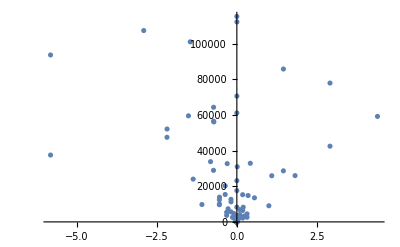

```mathematica
ListPlot[{Re[#],Im[#]}&/@Eigenvalues[A[0.5,1.0, 1000]],PlotRange->All]
```

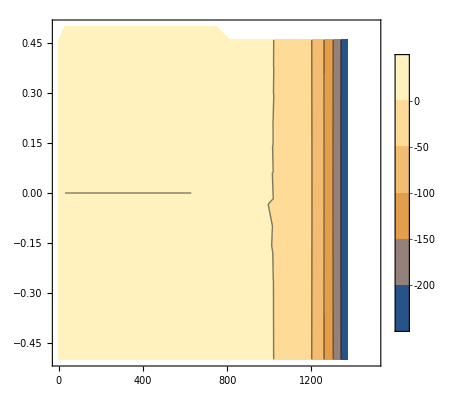

```mathematica
num=50;
Monitor[
vals=Table[{ad,k,MinimalBy[{Re[#],Im[#]}&/@Eigenvalues[A[k,1.0,ad]],#[[2]]&][[1,2]]},{ad,0,1500,1500/num},{k,-1/2,1/2,1.0/num}];,{ad,k}]
ListContourPlot[Flatten[vals,1],PlotLegends->True]
```

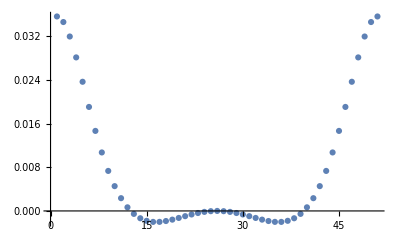

```mathematica
ListPlot[vals[[num/2+10,All,3]]]
```

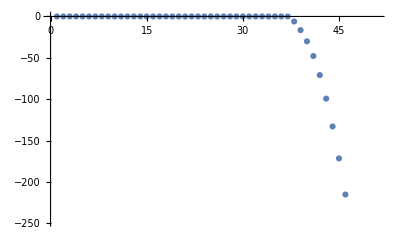

```mathematica
ListPlot[vals[[All,num/2+1,3]]]
```